```mathematica
(* JSQ system time distribution solver *)
B=5;
λ=5/4;
μ={1,11/10,12/10,13/10,14/10};
i0=4;
ν[0]=0;
ν[1]=0;
ν[2]=0;
ν[3]=1/2;
ν[4]=1/2;
ν[5]=0;
eqns={};
z0=ν[i0-1]μ[[i0-1]];

eqns={};
For[j=1,j≤i0,j++,
For[i=1,i≤j,i++,
eqn={};
If[(j<i0-1),
eqn={Hs[i,j]==Hs[i,j+1]}];
If[(i==1)&&(j==i0-1),
eqn={Hs[1,i0-1]==
((λ-z0)/ν[i0-1]+μ[[i0-1]])/(s+(λ-z0)/ν[i0-1]+μ[[i0-1]])*
(μ[[i0-1]]/((λ-z0)/ν[i0-1]+μ[[i0-1]])+((λ-z0)/ν[i0-1])/((λ-z0)/ν[i0-1]+μ[[i0-1]])Hs[1,i0])}];
If[(i>1)&&(j==i0-1),
eqn={Hs[i,i0-1]==
((λ-z0)/ν[i0-1]+μ[[i0-1]])/(s+(λ-z0)/ν[i0-1]+μ[[i0-1]])*
(((λ-z0)/ν[i0-1])/((λ-z0)/ν[i0-1]+μ[[i0-1]])Hs[i,i0]+μ[[i0-1]]/((λ-z0)/ν[i0-1]+μ[[i0-1]])*Hs[i-1,i0-2])}];
If[(i==1)&&(j>i0-1),
eqn={Hs[1,j]==
μ[[j]]/(s+μ[[j]])}];
If[(i>1)&&(j>i0-1),
eqn={Hs[i,j]==
μ[[j]]/(s+μ[[j]])*Hs[i-1,j-1]}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
eqns
{Hs3,Hs4}={Hs[3,3],Hs[4,4]}/.Solve[eqns][[1]];
Hssol=μ[[3]]ν[3]/λ*Hs3+μ[[4]]ν[4]/λ*Hs4
```

{Hs[1,1]==Hs[1,2],Hs[1,2]==Hs[1,3],Hs[2,2]==Hs[2,3],Hs[1,3]==(5 (12/25+13/25 Hs[1,4]))/(2 (5/2+s)),Hs[2,3]==(5 (12/25 Hs[1,2]+13/25 Hs[2,4]))/(2 (5/2+s)),Hs[3,3]==(5 (12/25 Hs[2,2]+13/25 Hs[3,4]))/(2 (5/2+s)),Hs[1,4]==13/(10 (13/10+s)),Hs[2,4]==(13 Hs[1,3])/(10 (13/10+s)),Hs[3,4]==(13 Hs[2,3])/(10 (13/10+s)),Hs[4,4]==(13 Hs[3,3])/(10 (13/10+s))}

(12 (65+24 s)^3)/(25 (65+76 s+20 s^2)^3)+1/25 ((25 (65+24 s)^4)/((65+76 s+20 s^2)^4)+(10 s (65+24 s)^4)/((65+76 s+20 s^2)^4)-(12 (65+24 s)^3)/((65+76 s+20 s^2)^3))

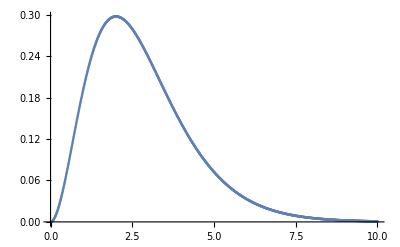

D:\Kut2\MM\hist_jsq.csv

```mathematica
Ht=ILT[Function[s,(12 (65+24 s)^3)/(25 (65+76 s+20 s^2)^3)+1/25 ((25 (65+24 s)^4)/((65+76 s+20 s^2)^4)+(10 s (65+24 s)^4)/((65+76 s+20 s^2)^4)-(12 (65+24 s)^3)/((65+76 s+20 s^2)^3))],Table[t,{t,1/100,10,1/100}],60,"cme",100];
Htlist = Table[{i/100,Ht[[i]]},{i,1,1000}];
ListPlot[Htlist]
Export["D:\\Kut2\\MM\\hist_jsq.csv",N[Htlist,6],"Table","FieldSeparator"->","]
```

```mathematica
(* random system time distribution solver *)
B=5;
λ=5/4;
μ={1,11/10,12/10,13/10,14/10};
c=1/Sum[∏_(j=1)^i λ/μ[[j]],{i,0,B}];
{ν[0],ν[1],ν[2],ν[3],ν[4],ν[5]}=c*Table[∏_(j=1)^i λ/μ[[j]],{i,0,B}];eqns={};
For[j=1,j≤B,j++,
For[i=1,i≤j,i++,
eqn={};
If[(i>1&&j≤B-1),
eqn={Hs[i,j]==
(λ+μ[[j]])/(s+λ+μ[[j]])*
(λ/(λ+μ[[j]])Hs[i,j+1]+μ[[j]]/(λ+μ[[j]])Hs[i-1,j-1])}];
If[(i>1)&&(j==B),
eqn={Hs[i,B]==
μ[[B]]/(s+μ[[B]])*Hs[i-1,B-1]}];
If[(i==1)&&(j≤B-1),
eqn={Hs[1,j]==(λ+μ[[j]])/(s+λ+μ[[j]])*(λ/(λ+μ[[j]])*Hs[i,j+1]+
μ[[j]]/(λ+μ[[j]]))}];
If[(i==1)&&(j==B),
eqn={Hs[1,B]==
μ[[B]]/(s+μ[[B]])}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
eqns
{Hs1,Hs2,Hs3,Hs4,Hs5}={Hs[1,1],Hs[2,2],Hs[3,3],Hs[4,4],Hs[5,5]}/.Solve[eqns][[1]];
Hssol=ν[0]*Hs1+ν[1]*Hs2+ν[2]*Hs3+ν[3]*Hs4+ν[4]*Hs5;
```

{Hs[1,1]==(9 (4/9+5/9 Hs[1,2]))/(4 (9/4+s)),Hs[1,2]==(47 (22/47+25/47 Hs[1,3]))/(20 (47/20+s)),Hs[2,2]==(47 (22/47 Hs[1,1]+25/47 Hs[2,3]))/(20 (47/20+s)),Hs[1,3]==(49 (24/49+25/49 Hs[1,4]))/(20 (49/20+s)),Hs[2,3]==(49 (24/49 Hs[1,2]+25/49 Hs[2,4]))/(20 (49/20+s)),Hs[3,3]==(49 (24/49 Hs[2,2]+25/49 Hs[3,4]))/(20 (49/20+s)),Hs[1,4]==(51 (26/51+25/51 Hs[1,5]))/(20 (51/20+s)),Hs[2,4]==(51 (26/51 Hs[1,3]+25/51 Hs[2,5]))/(20 (51/20+s)),Hs[3,4]==(51 (26/51 Hs[2,3]+25/51 Hs[3,5]))/(20 (51/20+s)),Hs[4,4]==(51 (26/51 Hs[3,3]+25/51 Hs[4,5]))/(20 (51/20+s)),Hs[1,5]==7/(5 (7/5+s)),Hs[2,5]==(7 Hs[1,4])/(5 (7/5+s)),Hs[3,5]==(7 Hs[2,4])/(5 (7/5+s)),Hs[4,5]==(7 Hs[3,4])/(5 (7/5+s)),Hs[5,5]==(7 Hs[4,4])/(5 (7/5+s))}

```mathematica
Hssol
```

(1537536 (7399539+10886200 s+6234000 s^2+1620000 s^3+160000 s^4))/(12059081 (7399539+17644809 s+16564000 s^2+7676000 s^3+1760000 s^4+160000 s^5))+(4 (-7570920246650239404032367577620192-5170911081964869309950403799984000 s-938379837667278616281194815283200 s^2+(1178409309987233179349332326747 (822171+901140 s+341600 s^2+44000 s^3)^5)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^5)+(1444555460073066104422338028020 s (822171+901140 s+341600 s^2+44000 s^3)^5)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^5)+(589942082596862668009678261200 s^2 (822171+901140 s+341600 s^2+44000 s^3)^5)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^5)+(80264228924743220137371192000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^5)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^5)+(9492410130459962447520905011284 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)+(12990410260114531823123584068960 s (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)+(5935130427210987385847594306400 s^2 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)+(901500585801078707742650016000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)+(1116983470591754909685186003813552 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(1753944606073811277057923764745280 s (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(884237630248065424007480513539200 s^2 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(144872146193292440230330010688000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(9322515137000620649670279854666656 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(14866529070517750122533572132784240 s (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(7319352734883018738964718434217600 s^2 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(1157133751323650652984490628704000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(2433719456903307230287279309213672 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(4675631633065594660018727908898720 s (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(4269420901668243405362135146908800 s^2 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(853072579697526014801086195712000 s^3 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(444585922195893230438232421875000 (7399539+10886200 s+6234000 s^2+1620000 s^3+160000 s^4))/(7399539+17644809 s+16564000 s^2+7676000 s^3+1760000 s^4+160000 s^5)))/20811659198570472650665283203125+1/69191616668853875 18304 (115064022338928+84524653248000 s+16398300828800 s^2-(184245277614069 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(287462314510790 s (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(143794593202400 s^2 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(23330922284000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(63156650456391 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(49761774089980 s (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(65880840836400 s^2 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(14907546208000 s^3 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(6627065300625 (7399539+10886200 s+6234000 s^2+1620000 s^3+160000 s^4))/(7399539+17644809 s+16564000 s^2+7676000 s^3+1760000 s^4+160000 s^5))+1/1044663677418439411484375 2496 (84483024746311553849904+57859615795231096308000 s+10290714512448702358400 s^2+(4769472450978934772059 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(7286322804352190608940 s (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(3587975265010235296400 s^2 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(574917485472029224000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)-(107245873001756224306718 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(154824818007834924817940 s (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(71016060035142977652800 s^2 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(10339109533482542824000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(13066362987056702481630 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(63877564621838374643640 s (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(50454254406360151652000 s^2 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(9355195011317002144000 s^3 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(5002813014599941406250 (7399539+10886200 s+6234000 s^2+1620000 s^3+160000 s^4))/(7399539+17644809 s+16564000 s^2+7676000 s^3+1760000 s^4+160000 s^5))+1/33298654717712756241064453125 104 (296704645968280600310493665592+201519993157241526239238284000 s+36598718899100013424329123200 s^2-(164139142244132259564284589 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)-(295448497014731758054453740 s (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)-(160738214748379094033684400 s^2 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)-(27547804645015934807304000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)-(63791331790421148859447721940 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)-(99858933937009362003495743640 s (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)-(50216902035150437494077324000 s^2 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)-(8209416851577272004888144000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)-(354504329690967983722017505844 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(582624749520566703318896908180 s (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(291729826867340527983889482400 s^2 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(46912958927231628627105128000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(104540219246448746836444049906 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(175464339253349283633807019720 s (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(164413598468052806385026682400 s^2 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(33271562635545466749390112000 s^3 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(17275338691040422668457031250 (7399539+10886200 s+6234000 s^2+1620000 s^3+160000 s^4))/(7399539+17644809 s+16564000 s^2+7676000 s^3+1760000 s^4+160000 s^5))

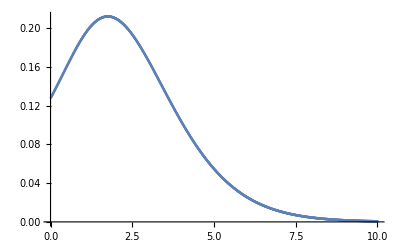

0.998869635356750394219299414340237846719181083717182537939831189348129580443932001

D:\Kut2\MM\hist_random.csv

```mathematica
Ht=ILT[Function[s,(1537536 (7399539+10886200 s+6234000 s^2+1620000 s^3+160000 s^4))/(12059081 (7399539+17644809 s+16564000 s^2+7676000 s^3+1760000 s^4+160000 s^5))+(4 (-7570920246650239404032367577620192-5170911081964869309950403799984000 s-938379837667278616281194815283200 s^2+(1178409309987233179349332326747 (822171+901140 s+341600 s^2+44000 s^3)^5)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^5)+(1444555460073066104422338028020 s (822171+901140 s+341600 s^2+44000 s^3)^5)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^5)+(589942082596862668009678261200 s^2 (822171+901140 s+341600 s^2+44000 s^3)^5)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^5)+(80264228924743220137371192000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^5)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^5)+(9492410130459962447520905011284 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)+(12990410260114531823123584068960 s (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)+(5935130427210987385847594306400 s^2 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)+(901500585801078707742650016000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)+(1116983470591754909685186003813552 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(1753944606073811277057923764745280 s (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(884237630248065424007480513539200 s^2 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(144872146193292440230330010688000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(9322515137000620649670279854666656 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(14866529070517750122533572132784240 s (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(7319352734883018738964718434217600 s^2 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(1157133751323650652984490628704000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(2433719456903307230287279309213672 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(4675631633065594660018727908898720 s (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(4269420901668243405362135146908800 s^2 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(853072579697526014801086195712000 s^3 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(444585922195893230438232421875000 (7399539+10886200 s+6234000 s^2+1620000 s^3+160000 s^4))/(7399539+17644809 s+16564000 s^2+7676000 s^3+1760000 s^4+160000 s^5)))/20811659198570472650665283203125+1/69191616668853875 18304 (115064022338928+84524653248000 s+16398300828800 s^2-(184245277614069 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(287462314510790 s (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(143794593202400 s^2 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(23330922284000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(63156650456391 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(49761774089980 s (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(65880840836400 s^2 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(14907546208000 s^3 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(6627065300625 (7399539+10886200 s+6234000 s^2+1620000 s^3+160000 s^4))/(7399539+17644809 s+16564000 s^2+7676000 s^3+1760000 s^4+160000 s^5))+1/1044663677418439411484375 2496 (84483024746311553849904+57859615795231096308000 s+10290714512448702358400 s^2+(4769472450978934772059 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(7286322804352190608940 s (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(3587975265010235296400 s^2 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)+(574917485472029224000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)-(107245873001756224306718 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(154824818007834924817940 s (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(71016060035142977652800 s^2 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(10339109533482542824000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(13066362987056702481630 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(63877564621838374643640 s (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(50454254406360151652000 s^2 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(9355195011317002144000 s^3 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(5002813014599941406250 (7399539+10886200 s+6234000 s^2+1620000 s^3+160000 s^4))/(7399539+17644809 s+16564000 s^2+7676000 s^3+1760000 s^4+160000 s^5))+1/33298654717712756241064453125 104 (296704645968280600310493665592+201519993157241526239238284000 s+36598718899100013424329123200 s^2-(164139142244132259564284589 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)-(295448497014731758054453740 s (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)-(160738214748379094033684400 s^2 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)-(27547804645015934807304000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^4)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^4)-(63791331790421148859447721940 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)-(99858933937009362003495743640 s (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)-(50216902035150437494077324000 s^2 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)-(8209416851577272004888144000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^3)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^3)-(354504329690967983722017505844 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(582624749520566703318896908180 s (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(291729826867340527983889482400 s^2 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)-(46912958927231628627105128000 s^3 (822171+901140 s+341600 s^2+44000 s^3)^2)/((822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)^2)+(104540219246448746836444049906 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(175464339253349283633807019720 s (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(164413598468052806385026682400 s^2 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)-(33271562635545466749390112000 s^3 (822171+901140 s+341600 s^2+44000 s^3))/(822171+1595125 s+1131500 s^2+350000 s^3+40000 s^4)+(17275338691040422668457031250 (7399539+10886200 s+6234000 s^2+1620000 s^3+160000 s^4))/(7399539+17644809 s+16564000 s^2+7676000 s^3+1760000 s^4+160000 s^5))],Table[t,{t,1/100,10,1/100}],60,"cme",100];
Htlist = Table[{i/100,Ht[[i]]},{i,1,1000}];
ListPlot[Htlist]
Sum[Ht[[i]],{i,1,1000}]/100+ν[5]
Export["D:\\Kut2\\MM\\hist_random.csv",N[Htlist,6],"Table","FieldSeparator"->","]
```

```mathematica
(* JIQ system time distribution solver *)
B=5;
λ=5/4;
μ={1,11/10,12/10,13/10,14/10};
{ν[0],ν[1],ν[2],ν[3],ν[4],ν[5]}={0, 29129,25387,20283,14958,10243}/100000;
eqns={};
z1=ν[1]μ[[1]];
eqns={};
For[j=1,j≤B,j++,
For[i=1,i≤j,i++,
eqn={};
If[(i==1)&&(j==B),
eqn={Hs[1,B]==μ[[B]]/(s+μ[[B]])}];
If[(i>1)&&(j==B),
eqn={Hs[i,B]==μ[[B]]/(s+μ[[B]])Hs[i-1,B-1]}];
If[(i==1)&&(j≤B-1),
eqn={Hs[1,j]==
((λ-z1)+μ[[j]])/(s+(λ-z1)+μ[[j]])((λ-z1)/((λ-z1)+μ[[j]])Hs[1,j+1]+μ[[j]]/((λ-z1)+μ[[j]]))}];
If[(i>1)&&(j≤B-1),
eqn={Hs[i,j]==((λ-z1)+μ[[j]])/(s+(λ-z1)+μ[[j]])*((λ-z1)/((λ-z1)+μ[[j]])*Hs[i,j+1]+μ[[j]]/((λ-z1)+μ[[j]])*Hs[i-1,j-1])}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
eqns
```

{Hs[1,1]==(195871 (100000/195871+(95871 Hs[1,2])/195871))/(100000 (195871/100000+s)),Hs[1,2]==(205871 (110000/205871+(95871 Hs[1,3])/205871))/(100000 (205871/100000+s)),Hs[2,2]==(205871 ((110000 Hs[1,1])/205871+(95871 Hs[2,3])/205871))/(100000 (205871/100000+s)),Hs[1,3]==(215871 (40000/71957+(31957 Hs[1,4])/71957))/(100000 (215871/100000+s)),Hs[2,3]==(215871 ((40000 Hs[1,2])/71957+(31957 Hs[2,4])/71957))/(100000 (215871/100000+s)),Hs[3,3]==(215871 ((40000 Hs[2,2])/71957+(31957 Hs[3,4])/71957))/(100000 (215871/100000+s)),Hs[1,4]==(225871 (130000/225871+(95871 Hs[1,5])/225871))/(100000 (225871/100000+s)),Hs[2,4]==(225871 ((130000 Hs[1,3])/225871+(95871 Hs[2,5])/225871))/(100000 (225871/100000+s)),Hs[3,4]==(225871 ((130000 Hs[2,3])/225871+(95871 Hs[3,5])/225871))/(100000 (225871/100000+s)),Hs[4,4]==(225871 ((130000 Hs[3,3])/225871+(95871 Hs[4,5])/225871))/(100000 (225871/100000+s)),Hs[1,5]==7/(5 (7/5+s)),Hs[2,5]==(7 Hs[1,4])/(5 (7/5+s)),Hs[3,5]==(7 Hs[2,4])/(5 (7/5+s)),Hs[4,5]==(7 Hs[3,4])/(5 (7/5+s)),Hs[5,5]==(7 Hs[4,4])/(5 (7/5+s))}

```mathematica
{Hs1,Hs2,Hs3,Hs4,Hs5}={Hs[1,1],Hs[2,2],Hs[3,3],Hs[4,4],Hs[5,5]}/.Solve[eqns][[1]];
Hssol=(μ[[1]]ν[1])/λ*Hs1+(1-(μ[[1]]ν[1])/λ)*(ν[1]*Hs2+ν[2]*Hs3+ν[3]*Hs4+ν[4]*Hs5)
```

(29129 (13763159174631911848167+23220527265144515300000 s+15137279515120000000000 s^2+4465355500000000000000 s^3+500000000000000000000 s^4))/(125000 (13763159174631911848167+36011816464777607834405 s+37359169088432622000000 s^2+19231861592300000000000 s^3+4917420000000000000000 s^4+500000000000000000000 s^5))+1/125000 95871 ((277 (-218430962497677052646142670618986807683037619801570503030157084246011854181977147992355261036646961921356000000000-168780850753465154004211438855031391716361971252674082458173252175994400790045064064512263101909775600000000000000 s-34520030674032302681640572643406828206652950460713187086627471509649293906269411619179953192520000000000000000000 s^2+(12480141849919709430114284929768890023357985518474110574078354645206830673635211042070936442864433113725650023 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^5)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^5+(17368754138363094280071055383729481163625672675674617724486060082129592907361788274132991786128346726413900000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^5)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^5+(8051654440000044448399976715599731898462895942483345868535823641022222621799925856123205505973603090000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^5)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^5+(1243281780940167113445835200281608290516542432360583538090776998148928854392967073873317167193000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^5)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^5+(357446219408386233248840517757902849594699537807230655625686699135915125408007902863460750095799352675745920000 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4+(558171818701936471618853637013268606838293162989293325439641857409881632552334642002982251037961624026000000000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4+(289182294041862646773006937316653574497109332287081089011061923197739915848407154273753223460684100000000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4+(49675680878232889976351664965424834110255751088962324609382217587205253602818336879915063740000000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4+(37768712740630968813908834475437604554561086344869206054971995287359939686890228073548649297079751938247200000000 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(63738651770628433763221942525553372200483478044503528247026499238100668685918870549129358646185746360000000000000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(35113453987359163706518073257564488125693360986249966148143240933241296163041786600421982105954000000000000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(6352177375165334085073645415206368863478341577272428532034522171481033691087837757346375800000000000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(208202049241061333139562229233169198193372045883455638091390905145222437580367556539322756236668548645629919280000 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2+(364596182859888286036830451251234864874609037714897063300711608977766360495590381220213674030535086675843085200000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2+(199351360225344300390804435589682202034532077362298039530563287602653750577987758725230769426220008248240000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2+(35296659658641729988412579778130355997537014709367773765424217636927015949142946865847329932000772000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(18915529813118065304360095361692566090971165585484190724857721262764492615203245250766030841254810609855210760000 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(169854468529283719470160486171682150082465916174996544587320127351044470799253648011055963353500707958644000000000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(146395743039659886069792536045015895172170617226129674576733985061502513067139125198666144911600694800000000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(31381846067302093346945975130369843824229954964284715533297701372408449005699465108345411993200000000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(8981663202365795156905707106994349432395117960111604521777724033045437101077259070530530176264361016418708520000 (13763159174631911848167+23220527265144515300000 s+15137279515120000000000 s^2+4465355500000000000000 s^3+500000000000000000000 s^4))/(13763159174631911848167+36011816464777607834405 s+37359169088432622000000 s^2+19231861592300000000000 s^3+4917420000000000000000 s^4+500000000000000000000 s^5)))/23208944054990349521380414112502372494974823118982658833585082484658009410695209490954011334871892660502907450000+(29129 (13412761422505366152598885146636971357100000+11245544599437643154915915525504710000000000 s+2474960660519235520804131157000000000000000 s^2-(17397329697242313958958589022524545862086211 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(29178735884366222098312443088783103361732570 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(15954935531862632047986640485060263934000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(2859029002137756193209679269197700000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2+(3499001259844125274997933683325839669492341 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(8435259400634540664444028179835879942900000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(9357154465520404403969760175677930000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(2249964236835668655276482870000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(534123716382104784497947211817908319043257 (13763159174631911848167+23220527265144515300000 s+15137279515120000000000 s^2+4465355500000000000000 s^3+500000000000000000000 s^4))/(13763159174631911848167+36011816464777607834405 s+37359169088432622000000 s^2+19231861592300000000000 s^3+4917420000000000000000 s^4+500000000000000000000 s^5)))/4855670148928225313617701925617348354938700000+(25387 (13885885621890309687445544753005202884575699615217100485938219686659800000+10698421468673182439517829289158767933180489924786725094087027980000000000 s+2114035537025288166195496275636137468797877298444642444266000000000000000 s^2+(952823155527628391607971184423763587112934257493650466116055643362042001 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(1573261624976909324521698761496709304684043952014081924407393430009300000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(849319166933200284757686369086685822075714746448340095715168830000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(150547992042621496479397179851183787421475156236447885791000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3-(13002232483466216943792428909035847525481918676882376884659503316093438924 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(19493088971668315338741124323955718104297736293922954948651892426789120660 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(9401619627593394667987888456380498302161775178483574380287821444092000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(1433777462667396873927370103876009610886020069730160118311142600000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(2418432192762342192400946024164052188061615852851424723332604584376783142 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(14127686797998063277167245755469224381631030423731032328072036967340200000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(10095218274017060102138433619747016641639302843878831014720028340000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(1921850488204807423814087523305579517088979362222402222060000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(590909066484630611865087595705870676344976051746482204490722302301432066 (13763159174631911848167+23220527265144515300000 s+15137279515120000000000 s^2+4465355500000000000000 s^3+500000000000000000000 s^4))/(13763159174631911848167+36011816464777607834405 s+37359169088432622000000 s^2+19231861592300000000000 s^3+4917420000000000000000 s^4+500000000000000000000 s^5)))/895316767400955472522859993493743449007539472343154855288973185305200100000+(6761 (12820212201747734528343907642048102628497250162085652074220653373049732478754956930659029800000+9817362335377949658424138237079084827908826048463951946110338927615165244715384564980000000000 s+2012095492688382023539100967317125136331334825856016738965863121902675773862166000000000000000 s^2-(18302070225084762800158508011982561889615171481712757279025622071335382622515718843925991119 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4-(31430619997939182614737964644596064392712284203305270338542762143649268834107394881006700000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4-(17463090820853494839680332534202689206211846032257920144760978943091022188218280770000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4-(3164223500214329413676111742661203507109877024212810158741009155365871622129000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4-(3625144352357694610859880487108462363071645730023333447253901389850015704747324326385128420000 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3-(6106238885753195687091190098663931700732734231255901636609901879756166265020046606841000000000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3-(3357615909849598461255565029332247504944073513612090130079183058926291519860130100000000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3-(606253969635321599967874051758366797575904927249504954993326156449835441530000000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3-(11708047542862887071195665178515105350826041166235114792851425212858469450909029884842862279524 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(21774397370506964128425448271523069337541636736865499523969774507639270398443551060200778999660 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(12336759646074743673618747224479013683653009020318169696200558278964602024482618161093892000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(2259400733347139777561335127546974563499026519841109050243369479147984111963088332600000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2+(2023421978356788719877898391532506990868250027659374327810116007255718756564302340342394059558 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(9112712088751193425855502921325238260549703700151705658384462901816999893011124075094970200000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(8292206720664558641186785146808290477436527350080966172078302609729769564811019499340000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(1829177720625801839581000879379204669392122568960015217241693747184250703511060000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(509641749500234927148403045809519395567141533707398225512718222876033756654205784190038419966 (13763159174631911848167+23220527265144515300000 s+15137279515120000000000 s^2+4465355500000000000000 s^3+500000000000000000000 s^4))/(13763159174631911848167+36011816464777607834405 s+37359169088432622000000 s^2+19231861592300000000000 s^3+4917420000000000000000 s^4+500000000000000000000 s^5)))/59398805303057683816830191819291304844655190408787671971179280055481789819837503984852962700000)

```mathematica
Ht=ILT[Function[s,(29129 (13763159174631911848167+23220527265144515300000 s+15137279515120000000000 s^2+4465355500000000000000 s^3+500000000000000000000 s^4))/(125000 (13763159174631911848167+36011816464777607834405 s+37359169088432622000000 s^2+19231861592300000000000 s^3+4917420000000000000000 s^4+500000000000000000000 s^5))+1/125000 95871 ((277 (-218430962497677052646142670618986807683037619801570503030157084246011854181977147992355261036646961921356000000000-168780850753465154004211438855031391716361971252674082458173252175994400790045064064512263101909775600000000000000 s-34520030674032302681640572643406828206652950460713187086627471509649293906269411619179953192520000000000000000000 s^2+(12480141849919709430114284929768890023357985518474110574078354645206830673635211042070936442864433113725650023 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^5)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^5+(17368754138363094280071055383729481163625672675674617724486060082129592907361788274132991786128346726413900000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^5)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^5+(8051654440000044448399976715599731898462895942483345868535823641022222621799925856123205505973603090000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^5)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^5+(1243281780940167113445835200281608290516542432360583538090776998148928854392967073873317167193000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^5)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^5+(357446219408386233248840517757902849594699537807230655625686699135915125408007902863460750095799352675745920000 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4+(558171818701936471618853637013268606838293162989293325439641857409881632552334642002982251037961624026000000000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4+(289182294041862646773006937316653574497109332287081089011061923197739915848407154273753223460684100000000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4+(49675680878232889976351664965424834110255751088962324609382217587205253602818336879915063740000000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4+(37768712740630968813908834475437604554561086344869206054971995287359939686890228073548649297079751938247200000000 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(63738651770628433763221942525553372200483478044503528247026499238100668685918870549129358646185746360000000000000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(35113453987359163706518073257564488125693360986249966148143240933241296163041786600421982105954000000000000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(6352177375165334085073645415206368863478341577272428532034522171481033691087837757346375800000000000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(208202049241061333139562229233169198193372045883455638091390905145222437580367556539322756236668548645629919280000 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2+(364596182859888286036830451251234864874609037714897063300711608977766360495590381220213674030535086675843085200000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2+(199351360225344300390804435589682202034532077362298039530563287602653750577987758725230769426220008248240000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2+(35296659658641729988412579778130355997537014709367773765424217636927015949142946865847329932000772000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(18915529813118065304360095361692566090971165585484190724857721262764492615203245250766030841254810609855210760000 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(169854468529283719470160486171682150082465916174996544587320127351044470799253648011055963353500707958644000000000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(146395743039659886069792536045015895172170617226129674576733985061502513067139125198666144911600694800000000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(31381846067302093346945975130369843824229954964284715533297701372408449005699465108345411993200000000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(8981663202365795156905707106994349432395117960111604521777724033045437101077259070530530176264361016418708520000 (13763159174631911848167+23220527265144515300000 s+15137279515120000000000 s^2+4465355500000000000000 s^3+500000000000000000000 s^4))/(13763159174631911848167+36011816464777607834405 s+37359169088432622000000 s^2+19231861592300000000000 s^3+4917420000000000000000 s^4+500000000000000000000 s^5)))/23208944054990349521380414112502372494974823118982658833585082484658009410695209490954011334871892660502907450000+(29129 (13412761422505366152598885146636971357100000+11245544599437643154915915525504710000000000 s+2474960660519235520804131157000000000000000 s^2-(17397329697242313958958589022524545862086211 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(29178735884366222098312443088783103361732570 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(15954935531862632047986640485060263934000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(2859029002137756193209679269197700000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2+(3499001259844125274997933683325839669492341 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(8435259400634540664444028179835879942900000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(9357154465520404403969760175677930000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(2249964236835668655276482870000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(534123716382104784497947211817908319043257 (13763159174631911848167+23220527265144515300000 s+15137279515120000000000 s^2+4465355500000000000000 s^3+500000000000000000000 s^4))/(13763159174631911848167+36011816464777607834405 s+37359169088432622000000 s^2+19231861592300000000000 s^3+4917420000000000000000 s^4+500000000000000000000 s^5)))/4855670148928225313617701925617348354938700000+(25387 (13885885621890309687445544753005202884575699615217100485938219686659800000+10698421468673182439517829289158767933180489924786725094087027980000000000 s+2114035537025288166195496275636137468797877298444642444266000000000000000 s^2+(952823155527628391607971184423763587112934257493650466116055643362042001 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(1573261624976909324521698761496709304684043952014081924407393430009300000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(849319166933200284757686369086685822075714746448340095715168830000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3+(150547992042621496479397179851183787421475156236447885791000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3-(13002232483466216943792428909035847525481918676882376884659503316093438924 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(19493088971668315338741124323955718104297736293922954948651892426789120660 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(9401619627593394667987888456380498302161775178483574380287821444092000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(1433777462667396873927370103876009610886020069730160118311142600000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(2418432192762342192400946024164052188061615852851424723332604584376783142 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(14127686797998063277167245755469224381631030423731032328072036967340200000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(10095218274017060102138433619747016641639302843878831014720028340000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(1921850488204807423814087523305579517088979362222402222060000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(590909066484630611865087595705870676344976051746482204490722302301432066 (13763159174631911848167+23220527265144515300000 s+15137279515120000000000 s^2+4465355500000000000000 s^3+500000000000000000000 s^4))/(13763159174631911848167+36011816464777607834405 s+37359169088432622000000 s^2+19231861592300000000000 s^3+4917420000000000000000 s^4+500000000000000000000 s^5)))/895316767400955472522859993493743449007539472343154855288973185305200100000+(6761 (12820212201747734528343907642048102628497250162085652074220653373049732478754956930659029800000+9817362335377949658424138237079084827908826048463951946110338927615165244715384564980000000000 s+2012095492688382023539100967317125136331334825856016738965863121902675773862166000000000000000 s^2-(18302070225084762800158508011982561889615171481712757279025622071335382622515718843925991119 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4-(31430619997939182614737964644596064392712284203305270338542762143649268834107394881006700000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4-(17463090820853494839680332534202689206211846032257920144760978943091022188218280770000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4-(3164223500214329413676111742661203507109877024212810158741009155365871622129000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^4)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^4-(3625144352357694610859880487108462363071645730023333447253901389850015704747324326385128420000 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3-(6106238885753195687091190098663931700732734231255901636609901879756166265020046606841000000000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3-(3357615909849598461255565029332247504944073513612090130079183058926291519860130100000000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3-(606253969635321599967874051758366797575904927249504954993326156449835441530000000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^3)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^3-(11708047542862887071195665178515105350826041166235114792851425212858469450909029884842862279524 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(21774397370506964128425448271523069337541636736865499523969774507639270398443551060200778999660 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(12336759646074743673618747224479013683653009020318169696200558278964602024482618161093892000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2-(2259400733347139777561335127546974563499026519841109050243369479147984111963088332600000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3)^2)/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)^2+(2023421978356788719877898391532506990868250027659374327810116007255718756564302340342394059558 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(9112712088751193425855502921325238260549703700151705658384462901816999893011124075094970200000 s (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(8292206720664558641186785146808290477436527350080966172078302609729769564811019499340000000000 s^2 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)-(1829177720625801839581000879379204669392122568960015217241693747184250703511060000000000000000 s^3 (70266446664549177+87851746053800000 s+37748070000000000 s^2+5500000000000000 s^3))/(70266446664549177+147980925192206555 s+115183342961500000 s^2+39380650000000000 s^3+5000000000000000 s^4)+(509641749500234927148403045809519395567141533707398225512718222876033756654205784190038419966 (13763159174631911848167+23220527265144515300000 s+15137279515120000000000 s^2+4465355500000000000000 s^3+500000000000000000000 s^4))/(13763159174631911848167+36011816464777607834405 s+37359169088432622000000 s^2+19231861592300000000000 s^3+4917420000000000000000 s^4+500000000000000000000 s^5)))/59398805303057683816830191819291304844655190408787671971179280055481789819837503984852962700000)],Table[t,{t,1/100,10,1/100}],60,"cme",100];
(Htlist = Table[{i/100,Ht[[i]]},{i,1,1000}];)
```

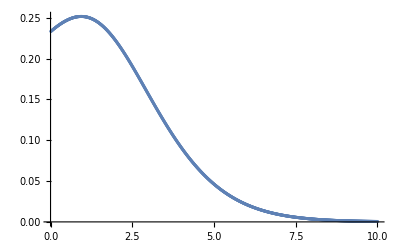

```mathematica
ListPlot[Htlist]
```

```mathematica
Export["D:\\Kut2\\MM\\hist_jiq.csv",N[Htlist,6],"Table","FieldSeparator"->","]
```

D:\Kut2\MM\hist_jiq.csv

```mathematica
(* JSQ(2) system time distribution solver *)
B=5;
d=2;
λ=5/4;
μ={1,11/10,12/10,13/10,14/10};
{ν[0],ν[1],ν[2],ν[3],ν[4],ν[5]}={028356,069885,148775,256443,308107,188434}/1000000;
z[5]=ν[5];
z[4]=ν[4]+ν[5];
z[3]=ν[3]+ν[4]+ν[5];
z[2]=ν[2]+ν[3]+ν[4]+ν[5];
z[1]=ν[1]+ν[2]+ν[3]+ν[4]+ν[5];
z[0]=1;
fpν[0]=(z[0]^d-z[1]^d)/ν[0];
fpν[1]=(z[1]^d-z[2]^d)/ν[1];
fpν[2]=(z[2]^d-z[3]^d)/ν[2];
fpν[3]=(z[3]^d-z[4]^d)/ν[3];
fpν[4]=(z[4]^d-z[5]^d)/ν[4];
eqns={};
For[j=1,j≤B,j++,
For[i=1,i≤j,i++,
eqn={};
If[(i>1&&j≤B-1),
eqn={Hs[i,j]==
(λ fpν[i]+μ[[j]])/(s+λ fpν[i]+μ[[j]])*
((λ fpν[i])/(λ fpν[i]+μ[[j]])Hs[i,j+1]+μ[[j]]/(λ fpν[i]+μ[[j]])Hs[i-1,j-1])}];
If[(i>1)&&(j==B),
eqn={Hs[i,B]==
μ[[B]]/(s+μ[[B]])*Hs[i-1,B-1]}];
If[(i==1)&&(j≤B-1),
eqn={Hs[1,j]==(λ fpν[i]+μ[[j]])/(s+λ fpν[i]+μ[[j]])*((λ fpν[i])/(λ fpν[i]+μ[[j]])*Hs[i,j+1]+
μ[[j]]/(λ fpν[i]+μ[[j]]))}];
If[(i==1)&&(j==B),
eqn={Hs[1,B]==
μ[[B]]/(s+μ[[B]])}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
eqns
{Hs1,Hs2,Hs3,Hs4,Hs5}={Hs[1,1],Hs[2,2],Hs[3,3],Hs[4,4],Hs[5,5]}/.Solve[eqns][[1]];
Hssol=ν[0]*Hs1+ν[1]*Hs2+ν[2]*Hs3+ν[3]*Hs4+ν[4]*Hs5
```

{Hs[1,1]==(2673403 (800000/2673403+(1873403 Hs[1,2])/2673403))/(800000 (2673403/800000+s)),Hs[1,2]==(2753403 (880000/2753403+(1873403 Hs[1,3])/2753403))/(800000 (2753403/800000+s)),Hs[2,2]==(2534743 ((880000 Hs[1,1])/2534743+(1654743 Hs[2,3])/2534743))/(800000 (2534743/800000+s)),Hs[1,3]==(2833403 (960000/2833403+(1873403 Hs[1,4])/2833403))/(800000 (2833403/800000+s)),Hs[2,3]==(2614743 ((320000 Hs[1,2])/871581+(551581 Hs[2,4])/871581))/(800000 (2614743/800000+s)),Hs[3,3]==(88381 ((38400 Hs[2,2])/88381+(49981 Hs[3,4])/88381))/(32000 (88381/32000+s)),Hs[1,4]==(2913403 (1040000/2913403+(1873403 Hs[1,5])/2913403))/(800000 (2913403/800000+s)),Hs[2,4]==(2694743 ((1040000 Hs[1,3])/2694743+(1654743 Hs[2,5])/2694743))/(800000 (2694743/800000+s)),Hs[3,4]==(91581 ((41600 Hs[2,3])/91581+(49981 Hs[3,5])/91581))/(32000 (91581/32000+s)),Hs[4,4]==(68999 ((41600 Hs[3,3])/68999+(27399 Hs[4,5])/68999))/(32000 (68999/32000+s)),Hs[1,5]==7/(5 (7/5+s)),Hs[2,5]==(7 Hs[1,4])/(5 (7/5+s)),Hs[3,5]==(7 Hs[2,4])/(5 (7/5+s)),Hs[4,5]==(7 Hs[3,4])/(5 (7/5+s)),Hs[5,5]==(7 Hs[4,4])/(5 (7/5+s))}

(7089 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(250000 (425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))+1/(200000 (-2534743-800000 s))13977 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))+(5951 (-68336450260318322571644276483238840608857482482056875564001884596411761784821162410842444034471044086991721784457067016303524383602145869873352903302008059520184039820259755634119521469739144710650931647159242643011431906341052642602191781685350400000000000-10702851660634728130231753484304228353300201001494019647306837153756265353781637402597980814610015322157992279304095974537080153762324416769546471956703678793151602544911696365662412541637891045477647157194932196163165695590353767918404976640000000000000000 s+947118687937761277674009909138848399483179608545543244649930679536120305742687970832904732843673764726338704976595374242491789237723113228724913071762794464579765474283295781879692389084887345570175691548511857077645616312250335232000000000000000000000 s^2-(2758406273893803175605511008173952475462399580262424888283035473393933509831978934442211026945365319122409291887785326626565495927194489805615178783120675815683756241335416283776746573941719996167993901006343186507496371181689181203508980971656320000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(2337717661146724717197409381799674165523171233302844523785771285997282692202491249750829923941853587048084968044951233179406337541620720917645677201284697439368608124299278662285159532706480245582192426459101483997416511721415417338939808256000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(660220668934806080262171562848044719892052998279971940416984296209690313349850973083305184576814976691773534272032820088549647032624995639422307436633178967184509876678120966981143372939610588150388492113851458388871073426169908621721600000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(62136888063322309393773406074890132220706855398964608085940879449876144301849610811527592752301970616654111377452749228970689735522973201192799606375154207825667333749381547393118769003407853915157944197734569433657085224720465920000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(764412872778018662881942430833002532532008658496866528938098379701374918039668653517760498256482695437695247867703270072757475822442253368993065541602409629992945021606912683820865681015773201964159624410958444317331260878039403710942662228309539263407 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(648170096593386832288140168487070877702124987465858360049377419778896714420196928864603768316527059600169510004859342242197178603249777825600549909040441732328550433831711520890815621225596092303702106668228645460681426093059041795309759062943045600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(183120193249654920106393937390185596969122579856684422404037917156666635088426419902496992912880117328352177011165824233969555181104265712944857083362514644853104211197788426943650752876248150657160867715698070641803975168766048483723941164160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(17238710202508671975476009974206187952340829160330927206144261649959956686394836226684096322411803444128605271725491922752339235373111408565633729813459706016023346003747162359386203380479328111832529039810639047123890805801467394836992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(8256243396785221355997898044998611727338795129103842190062994452850861841234357073112431215784389035795230827267131466769679402964890338179957669022855381337053819382200424029957467106672688734292345636558045667589581089579413621411367780560525680960000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(6902563806178313979180319388655925913537526760932950632376445781248025416573154926793115823553051070643288720319710350379978432555607744182605104658230910075021545702534861998767886795863684464521738753855757332750737030085048093362708358219648000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(1931765580363573641919815204583372753141222045688620247894970982636509898514291538500830075578097502159238991331869422306156587255159027950510125446893027264485233167294368874355931435434529195022393007892405390613550899896023100012108236800000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(180610835298062785581173321921425605995248617878227094712945635036748232942807153015303916703132288571976228226033486593395268059978769769007243846706934538201364717923578591243183565650009812207571810717196384064788370347808631767040000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(187287046464164411380160743820333739698287426951547454665207494924028020924849505408405838148356453940239728067984980196036357628025379051358138347052735348269186393511972079673017398633089666339482088750808364294682909503121990298089800965669337903045760000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(158814594282300217978911136275519224385170540244291734072398141300015621446708486781453591545168604827965670432846992257896672607429502493104826484542144029610374121724498450966573770380079944323537896938287508279046526067060303761300953946516258136320000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(44877591745840119732194542251805674989627849135988167733005392439067454985840960812605771252930541098613106474228077159371514154946103345847398050044752135340930277500888605447498798234834730457062513240755368200302388255353585518022693298632704000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(4225963688875891763012906230104398760128424276338144267351373306567107000993108302206545323338901525151023845972477681888422141429912316809729223467690514579480265043516219929562719904770259012940411601564685316031013538035621378676769587200000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(155185546894966664919885624075931206878266639464317708899933456307298974458923457997032455393811933169750063893239139137856612082892547160680225529409892336439047564803878651337978203695397757414462036096337365038500760476925975788091059955971459186816000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(115996612393757306840885705904134005633851433603936693423374051387745567939313684402498540930344789534243925428731127461862759051444325091165557609862217381709673626157637629997753497916748423276295634866642377006544634778303326295213283934955417600000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(14377661384176467373473538234224606807891567181416673578801708213480228907198613263850463381187195769598940354156583962619364566258241051179694597157308852108064169377600350648121088559033223786745406159083993495177289617475520995175819755520000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(861016989034328434249099917398953090439254189586857495136300617760109368856989064393549757130612513387580640887813976584083444761566466571568102792511631331436150431166632528981538535531715768700159719589556233706950560283863941120000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(43684070589718390650425462281240700760525549891977966677028163315975497926677008406610149640105000501627282885365274484572731742463147864000810557713939244433825956786404848605815965476778473286295252108902939134546035512072085235187712000000000000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4)^2)/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)^2-(1335789746027188954010737658230705305330911903130398962943016228153969418318409834715779581001937183160986319189047664612202685516255043384407135437488333355736058158735653289568694385095443083399538108645458619291096279394384027621241517825156343168000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)+(101771535420675483756359544517156428338370056901367776353566228816862902303723602309733098874018881422364771795201479363957586841062280982249463241823203327197054276587246676727945105582243217631529066107044302741943981593764100172656447323848481886901760000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(31023527436110591177928259475635524806629507941258875219799743080967424710814940692383735945401579102703170122711612490683452272459491601331763082016130428009784963085345425566089462680133996907823526913476376590090214834588765314872590247451364096000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)-(555274386785806709206175118726540978339470581285995106754358222443239348577076144311764843880268972428583152796308039614003304772007732088996435640281874976732806958950909893115598884974918789669490076113449663963016173383432267885028727927138708223407 ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-(152828578881153992097045448565934227997629765424022853561511693290330516312471801568022774907013337407884745981999918531733467429325828067110672248089784115817199561628126321098245328405206603736061982094316856735682070831792617912251833839541639200000 s ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-1/(-2534743-800000 s)2757598800211863972120473059856979568061251520137201181148884001439425974313464607437904703621960922382051834408965187345717509024666657098937541142058586272333014357412315586119643245960410379281583493810047483255610313954625882501727764245611504000000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))+1/(-2534743-800000 s)^2 3628379694375556517472912911957931107127641928469516853907269082795879976621721564049910647278408210783484928800423008885838001025614909271006176220193046805649417381816693612364560595015987356079978772836903584705432325831038274135641402470400000000 ((-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))^2-(3638536152278950140994980008482880287052563206963266177746926650616938031054587150181758133747254970570483973959395938398227147542603848988795813158329553318823257716432936164745229301713649835671636366679236578846460434653698191657366953554329600000000 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)))/(40000 (-176492853003258022027735835396596286462565130226908066433402305366213081383506469748633182681413172107085426044688644901406236508822114001133931899006204955711233420730612969760383352958235993482256154959678041808879660015502245243722853851955200000000-1/(-2534743-800000 s)1229181653588989311978651866042848373747747346555207637702098163092406764830169837101233167590197251556857709973558302191494232309946280795102173560394523225041346064666314024193726737072822266635019308900491781261178427231373547331088568363144320000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))))+(256443 (-216475231396297831247560245042642907899626750655878998205121634855448548516431409722163200000000000000-301568268236738047130732506624561250480092585310783943466606399195513955480756551680000000000000000000 s-52598360951644852312956500787531959825204068775709956438756830302334645960704000000000000000000000000 s^2-(4714642989058881824166239253560525742399545456029271448068701294060680522354808985433419051184173074731 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(3995605827116405811544208111389317524096657234928381536716444817763924927841876593952368682274344800000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(1128443180210474558966191291793373556712213427661791733519085670210924125702831605165792241280000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(106203805596824695389601953720749553966234329312306719377755127687888533159862926209536000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(3838215726884263060040797291347563095271726006014899743750468961278055574788642923032082441263727241600 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(2673497350566883814639943215369389374906997761440718379396797336737484557292883500155609110049280000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(646832652414218742941715528919324227848109520656136486263594063444214191856115572653969408000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(53540597675435692828579270546228945840729594560806826726781305355986108780184402329600000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(390384854772645282453523791946568151450451938551521663924949383155258441710826052070783302982400000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(180065228852791157598586889378170111250814344887769103362097070394904426160846453170054144000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(163560221581290716771949790269502936309847016081076216667722615606157213681965169049600000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(23867570063366878726979014820756422697427044731793971556965798400131853718257664000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(859574172509842165615051008300039496230491066364027438940802549861063338040321274715280240640000000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(675792748703892895636206413439515020332817291202820299547376735942551104320472148492288000000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(342826121211575742620566930608057647529191790364802885377028707588103463509871820800000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(47816691774222593011778637079574508932003698887009051307960754820304223600640000000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(2401630212206049851181901024794488563621320752588992480704764737785762670304724487701555624665088000000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(201855677233133488761297864700332003298433388487193872793140313906807736424934988413443686400000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(2503521067816693011060641609372595537668673890793491942314771948643999178465617490153656757213684844800 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)-(3969185131772080588852466921797907363719783914709438053512264537505784967077528047137843450672793270400 (-68336450260318322571644276483238840608857482482056875564001884596411761784821162410842444034471044086991721784457067016303524383602145869873352903302008059520184039820259755634119521469739144710650931647159242643011431906341052642602191781685350400000000000-10702851660634728130231753484304228353300201001494019647306837153756265353781637402597980814610015322157992279304095974537080153762324416769546471956703678793151602544911696365662412541637891045477647157194932196163165695590353767918404976640000000000000000 s+947118687937761277674009909138848399483179608545543244649930679536120305742687970832904732843673764726338704976595374242491789237723113228724913071762794464579765474283295781879692389084887345570175691548511857077645616312250335232000000000000000000000 s^2-(2758406273893803175605511008173952475462399580262424888283035473393933509831978934442211026945365319122409291887785326626565495927194489805615178783120675815683756241335416283776746573941719996167993901006343186507496371181689181203508980971656320000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(2337717661146724717197409381799674165523171233302844523785771285997282692202491249750829923941853587048084968044951233179406337541620720917645677201284697439368608124299278662285159532706480245582192426459101483997416511721415417338939808256000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(660220668934806080262171562848044719892052998279971940416984296209690313349850973083305184576814976691773534272032820088549647032624995639422307436633178967184509876678120966981143372939610588150388492113851458388871073426169908621721600000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(62136888063322309393773406074890132220706855398964608085940879449876144301849610811527592752301970616654111377452749228970689735522973201192799606375154207825667333749381547393118769003407853915157944197734569433657085224720465920000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(764412872778018662881942430833002532532008658496866528938098379701374918039668653517760498256482695437695247867703270072757475822442253368993065541602409629992945021606912683820865681015773201964159624410958444317331260878039403710942662228309539263407 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(648170096593386832288140168487070877702124987465858360049377419778896714420196928864603768316527059600169510004859342242197178603249777825600549909040441732328550433831711520890815621225596092303702106668228645460681426093059041795309759062943045600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(183120193249654920106393937390185596969122579856684422404037917156666635088426419902496992912880117328352177011165824233969555181104265712944857083362514644853104211197788426943650752876248150657160867715698070641803975168766048483723941164160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(17238710202508671975476009974206187952340829160330927206144261649959956686394836226684096322411803444128605271725491922752339235373111408565633729813459706016023346003747162359386203380479328111832529039810639047123890805801467394836992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(8256243396785221355997898044998611727338795129103842190062994452850861841234357073112431215784389035795230827267131466769679402964890338179957669022855381337053819382200424029957467106672688734292345636558045667589581089579413621411367780560525680960000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(6902563806178313979180319388655925913537526760932950632376445781248025416573154926793115823553051070643288720319710350379978432555607744182605104658230910075021545702534861998767886795863684464521738753855757332750737030085048093362708358219648000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(1931765580363573641919815204583372753141222045688620247894970982636509898514291538500830075578097502159238991331869422306156587255159027950510125446893027264485233167294368874355931435434529195022393007892405390613550899896023100012108236800000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(180610835298062785581173321921425605995248617878227094712945635036748232942807153015303916703132288571976228226033486593395268059978769769007243846706934538201364717923578591243183565650009812207571810717196384064788370347808631767040000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(187287046464164411380160743820333739698287426951547454665207494924028020924849505408405838148356453940239728067984980196036357628025379051358138347052735348269186393511972079673017398633089666339482088750808364294682909503121990298089800965669337903045760000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(158814594282300217978911136275519224385170540244291734072398141300015621446708486781453591545168604827965670432846992257896672607429502493104826484542144029610374121724498450966573770380079944323537896938287508279046526067060303761300953946516258136320000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(44877591745840119732194542251805674989627849135988167733005392439067454985840960812605771252930541098613106474228077159371514154946103345847398050044752135340930277500888605447498798234834730457062513240755368200302388255353585518022693298632704000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(4225963688875891763012906230104398760128424276338144267351373306567107000993108302206545323338901525151023845972477681888422141429912316809729223467690514579480265043516219929562719904770259012940411601564685316031013538035621378676769587200000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(155185546894966664919885624075931206878266639464317708899933456307298974458923457997032455393811933169750063893239139137856612082892547160680225529409892336439047564803878651337978203695397757414462036096337365038500760476925975788091059955971459186816000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(115996612393757306840885705904134005633851433603936693423374051387745567939313684402498540930344789534243925428731127461862759051444325091165557609862217381709673626157637629997753497916748423276295634866642377006544634778303326295213283934955417600000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(14377661384176467373473538234224606807891567181416673578801708213480228907198613263850463381187195769598940354156583962619364566258241051179694597157308852108064169377600350648121088559033223786745406159083993495177289617475520995175819755520000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(861016989034328434249099917398953090439254189586857495136300617760109368856989064393549757130612513387580640887813976584083444761566466571568102792511631331436150431166632528981538535531715768700159719589556233706950560283863941120000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(43684070589718390650425462281240700760525549891977966677028163315975497926677008406610149640105000501627282885365274484572731742463147864000810557713939244433825956786404848605815965476778473286295252108902939134546035512072085235187712000000000000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4)^2)/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)^2-(1335789746027188954010737658230705305330911903130398962943016228153969418318409834715779581001937183160986319189047664612202685516255043384407135437488333355736058158735653289568694385095443083399538108645458619291096279394384027621241517825156343168000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)+(101771535420675483756359544517156428338370056901367776353566228816862902303723602309733098874018881422364771795201479363957586841062280982249463241823203327197054276587246676727945105582243217631529066107044302741943981593764100172656447323848481886901760000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(31023527436110591177928259475635524806629507941258875219799743080967424710814940692383735945401579102703170122711612490683452272459491601331763082016130428009784963085345425566089462680133996907823526913476376590090214834588765314872590247451364096000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)-(555274386785806709206175118726540978339470581285995106754358222443239348577076144311764843880268972428583152796308039614003304772007732088996435640281874976732806958950909893115598884974918789669490076113449663963016173383432267885028727927138708223407 ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-(152828578881153992097045448565934227997629765424022853561511693290330516312471801568022774907013337407884745981999918531733467429325828067110672248089784115817199561628126321098245328405206603736061982094316856735682070831792617912251833839541639200000 s ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-1/(-2534743-800000 s)2757598800211863972120473059856979568061251520137201181148884001439425974313464607437904703621960922382051834408965187345717509024666657098937541142058586272333014357412315586119643245960410379281583493810047483255610313954625882501727764245611504000000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))+1/(-2534743-800000 s)^2 3628379694375556517472912911957931107127641928469516853907269082795879976621721564049910647278408210783484928800423008885838001025614909271006176220193046805649417381816693612364560595015987356079978772836903584705432325831038274135641402470400000000 ((-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))^2-(3638536152278950140994980008482880287052563206963266177746926650616938031054587150181758133747254970570483973959395938398227147542603848988795813158329553318823257716432936164745229301713649835671636366679236578846460434653698191657366953554329600000000 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)))/(-176492853003258022027735835396596286462565130226908066433402305366213081383506469748633182681413172107085426044688644901406236508822114001133931899006204955711233420730612969760383352958235993482256154959678041808879660015502245243722853851955200000000-1/(-2534743-800000 s)1229181653588989311978651866042848373747747346555207637702098163092406764830169837101233167590197251556857709973558302191494232309946280795102173560394523225041346064666314024193726737072822266635019308900491781261178427231373547331088568363144320000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))))/(1000000 (-6583408771806292993995946277334947360319744479111454717651267808253885984215922060684232217619520741931-3053219332132369683732666862921467202861372242084183118086357336542911513136560036259879577440610208000 s))+(308107 (-87904278698746960619206439849348537040295997314501095617017219698870478806304085938443529730615039385543679976174857249294439428957143040000000000000000-36537709747604539957500978193872622412881956819222130289079694940454206273215665137181815020368253625344523777640498363191783325696000000000000000000000 s-4100828019685077908721016373006330763199898672745009436971376604287006591848794630590766769005797218815625085752502989409484800000000000000000000000000 s^2+(72908351214044164879515107967335108160871267019387011349472239768816577111500215877092792590466000000595293339107285080112232654428028389139731298106139 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(61788990944240104098192234231557844526743504109090630319732199377971699302264528204125742303301263298849649816763861767861883704705192681058761551200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(17450511501890242742608486273955956784546986252667246453774525434380309475069294149710325427932999997835686108254756070463719487913548278984320000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(1642360699779522385165681104919274976372650249203731009792773371514070722267586046386419480079419223488334097032650003825903056069661184000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(182610213306779395626514318185208228725078689173479036847710422325558975117743561607558830428938292679536366641196358442743031978934359694014780495436800 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(145800910268119519165636222060346130294552038728124215934462727356768889524356575247741779722020081960687957113535432714969555390088173264550077440000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(39503717415131508955147839181822080356258948475534564736486127161181274011055088857184255762550973918167748253376544038524533464769096566784000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(3604455664169007083226609510999557323008391794328345004288043703963755560554697324974201054912551096026315064290563439700839694109900800000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(124155051208080392528495758173392801456220435869938602636129000625242176924085711295330601454536681076924531809668674487558954772449169772886741831680000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(97974961630146771352212487509147179824819862977051254210520030927728233387579415443345666241031165231875586986303608110373806005122332393734144000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(26583922000322970970325847032129911149329837523821387904985912029802265402562566251271456468519062047215528476720855160862463223828604518400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(2441206771788029066741652759377365812721072789861125667445470357723462590328616288390167426370785651588216931014400837038549845934080000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(241367061559956601639316099674015893097175482266743134858476794978316309017528445611055175558189848671647901047981422087874294055169854927644262400000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(194600368565461874756701372932676331203059675338129769657444084474498805017154139236870389678342725202588114738999130017555367452609670021120000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(52962107601884690160540805017221477978556790129299856692245240094653664620071910926652170868760089328232531139731204351018829890977792000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(4839957769455410525549273119855400539386145344030892341324810592962344044555441969319774585348886159286524216106848834972916121600000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(66046024868668611301946016588276105825721357792843547227516708541590671593871094072992882632372765574836754052061710143805846173721224871936000000000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(54011529159627627298827491629003778356012713523367408963370829866100592685188506851169253006341177614817271590364222352111401243508736000000000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(31199327186544236621585507043421577996589006587279853029866443178412304609171335923002995917465500168384638609265587993895784939520000000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(3728025472440979917019105793642118875636271520677281306337615094806369628953449664173424335459815653468750077956820899463168000000000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31773548934490817675027732070407067942388428808575026900344219421716152978772602193090828311774611598022495181919796855809467680068766007296000000000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)-(123466546152489128420082730154456139165413621064380768497800126479647077415745443453765276049103465596217037479545109421560311369283830391088742400000000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)-(18407616675004999061757860707036641110799037551084698520482726919046134008132137537349711773282810431732804243066205445413994766209189150720000000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)-1/(-2534743-800000 s)56087643449414590510046709183371080185125014177871446036449331229945610438277609732447581786358655659321520548954270676369311957524842411399577600000000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))-(39741712441585084378750151203872143220331707696679323713268489463767659621592862298906485793731380968884554423747866204461750604235310623276713349120000 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)-(82655834329744943772869803635635366764941997846921232479108787721090565362791854610116759582477503732745318693738762249477864069504758466281950638080000 (-68336450260318322571644276483238840608857482482056875564001884596411761784821162410842444034471044086991721784457067016303524383602145869873352903302008059520184039820259755634119521469739144710650931647159242643011431906341052642602191781685350400000000000-10702851660634728130231753484304228353300201001494019647306837153756265353781637402597980814610015322157992279304095974537080153762324416769546471956703678793151602544911696365662412541637891045477647157194932196163165695590353767918404976640000000000000000 s+947118687937761277674009909138848399483179608545543244649930679536120305742687970832904732843673764726338704976595374242491789237723113228724913071762794464579765474283295781879692389084887345570175691548511857077645616312250335232000000000000000000000 s^2-(2758406273893803175605511008173952475462399580262424888283035473393933509831978934442211026945365319122409291887785326626565495927194489805615178783120675815683756241335416283776746573941719996167993901006343186507496371181689181203508980971656320000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(2337717661146724717197409381799674165523171233302844523785771285997282692202491249750829923941853587048084968044951233179406337541620720917645677201284697439368608124299278662285159532706480245582192426459101483997416511721415417338939808256000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(660220668934806080262171562848044719892052998279971940416984296209690313349850973083305184576814976691773534272032820088549647032624995639422307436633178967184509876678120966981143372939610588150388492113851458388871073426169908621721600000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(62136888063322309393773406074890132220706855398964608085940879449876144301849610811527592752301970616654111377452749228970689735522973201192799606375154207825667333749381547393118769003407853915157944197734569433657085224720465920000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(764412872778018662881942430833002532532008658496866528938098379701374918039668653517760498256482695437695247867703270072757475822442253368993065541602409629992945021606912683820865681015773201964159624410958444317331260878039403710942662228309539263407 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(648170096593386832288140168487070877702124987465858360049377419778896714420196928864603768316527059600169510004859342242197178603249777825600549909040441732328550433831711520890815621225596092303702106668228645460681426093059041795309759062943045600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(183120193249654920106393937390185596969122579856684422404037917156666635088426419902496992912880117328352177011165824233969555181104265712944857083362514644853104211197788426943650752876248150657160867715698070641803975168766048483723941164160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(17238710202508671975476009974206187952340829160330927206144261649959956686394836226684096322411803444128605271725491922752339235373111408565633729813459706016023346003747162359386203380479328111832529039810639047123890805801467394836992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(8256243396785221355997898044998611727338795129103842190062994452850861841234357073112431215784389035795230827267131466769679402964890338179957669022855381337053819382200424029957467106672688734292345636558045667589581089579413621411367780560525680960000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(6902563806178313979180319388655925913537526760932950632376445781248025416573154926793115823553051070643288720319710350379978432555607744182605104658230910075021545702534861998767886795863684464521738753855757332750737030085048093362708358219648000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(1931765580363573641919815204583372753141222045688620247894970982636509898514291538500830075578097502159238991331869422306156587255159027950510125446893027264485233167294368874355931435434529195022393007892405390613550899896023100012108236800000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(180610835298062785581173321921425605995248617878227094712945635036748232942807153015303916703132288571976228226033486593395268059978769769007243846706934538201364717923578591243183565650009812207571810717196384064788370347808631767040000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(187287046464164411380160743820333739698287426951547454665207494924028020924849505408405838148356453940239728067984980196036357628025379051358138347052735348269186393511972079673017398633089666339482088750808364294682909503121990298089800965669337903045760000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(158814594282300217978911136275519224385170540244291734072398141300015621446708486781453591545168604827965670432846992257896672607429502493104826484542144029610374121724498450966573770380079944323537896938287508279046526067060303761300953946516258136320000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(44877591745840119732194542251805674989627849135988167733005392439067454985840960812605771252930541098613106474228077159371514154946103345847398050044752135340930277500888605447498798234834730457062513240755368200302388255353585518022693298632704000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(4225963688875891763012906230104398760128424276338144267351373306567107000993108302206545323338901525151023845972477681888422141429912316809729223467690514579480265043516219929562719904770259012940411601564685316031013538035621378676769587200000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(155185546894966664919885624075931206878266639464317708899933456307298974458923457997032455393811933169750063893239139137856612082892547160680225529409892336439047564803878651337978203695397757414462036096337365038500760476925975788091059955971459186816000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(115996612393757306840885705904134005633851433603936693423374051387745567939313684402498540930344789534243925428731127461862759051444325091165557609862217381709673626157637629997753497916748423276295634866642377006544634778303326295213283934955417600000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(14377661384176467373473538234224606807891567181416673578801708213480228907198613263850463381187195769598940354156583962619364566258241051179694597157308852108064169377600350648121088559033223786745406159083993495177289617475520995175819755520000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(861016989034328434249099917398953090439254189586857495136300617760109368856989064393549757130612513387580640887813976584083444761566466571568102792511631331436150431166632528981538535531715768700159719589556233706950560283863941120000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(43684070589718390650425462281240700760525549891977966677028163315975497926677008406610149640105000501627282885365274484572731742463147864000810557713939244433825956786404848605815965476778473286295252108902939134546035512072085235187712000000000000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4)^2)/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)^2-(1335789746027188954010737658230705305330911903130398962943016228153969418318409834715779581001937183160986319189047664612202685516255043384407135437488333355736058158735653289568694385095443083399538108645458619291096279394384027621241517825156343168000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)+(101771535420675483756359544517156428338370056901367776353566228816862902303723602309733098874018881422364771795201479363957586841062280982249463241823203327197054276587246676727945105582243217631529066107044302741943981593764100172656447323848481886901760000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(31023527436110591177928259475635524806629507941258875219799743080967424710814940692383735945401579102703170122711612490683452272459491601331763082016130428009784963085345425566089462680133996907823526913476376590090214834588765314872590247451364096000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)-(555274386785806709206175118726540978339470581285995106754358222443239348577076144311764843880268972428583152796308039614003304772007732088996435640281874976732806958950909893115598884974918789669490076113449663963016173383432267885028727927138708223407 ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-(152828578881153992097045448565934227997629765424022853561511693290330516312471801568022774907013337407884745981999918531733467429325828067110672248089784115817199561628126321098245328405206603736061982094316856735682070831792617912251833839541639200000 s ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-1/(-2534743-800000 s)2757598800211863972120473059856979568061251520137201181148884001439425974313464607437904703621960922382051834408965187345717509024666657098937541142058586272333014357412315586119643245960410379281583493810047483255610313954625882501727764245611504000000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))+1/(-2534743-800000 s)^2 3628379694375556517472912911957931107127641928469516853907269082795879976621721564049910647278408210783484928800423008885838001025614909271006176220193046805649417381816693612364560595015987356079978772836903584705432325831038274135641402470400000000 ((-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))^2-(3638536152278950140994980008482880287052563206963266177746926650616938031054587150181758133747254970570483973959395938398227147542603848988795813158329553318823257716432936164745229301713649835671636366679236578846460434653698191657366953554329600000000 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)))/(-176492853003258022027735835396596286462565130226908066433402305366213081383506469748633182681413172107085426044688644901406236508822114001133931899006204955711233420730612969760383352958235993482256154959678041808879660015502245243722853851955200000000-1/(-2534743-800000 s)1229181653588989311978651866042848373747747346555207637702098163092406764830169837101233167590197251556857709973558302191494232309946280795102173560394523225041346064666314024193726737072822266635019308900491781261178427231373547331088568363144320000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))-(86591921055880153715515358467418868244782144427083515208462501867135767525861341725084098542402694475403214759418966288329201779160742276899848335532800 (-216475231396297831247560245042642907899626750655878998205121634855448548516431409722163200000000000000-301568268236738047130732506624561250480092585310783943466606399195513955480756551680000000000000000000 s-52598360951644852312956500787531959825204068775709956438756830302334645960704000000000000000000000000 s^2-(4714642989058881824166239253560525742399545456029271448068701294060680522354808985433419051184173074731 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(3995605827116405811544208111389317524096657234928381536716444817763924927841876593952368682274344800000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(1128443180210474558966191291793373556712213427661791733519085670210924125702831605165792241280000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(106203805596824695389601953720749553966234329312306719377755127687888533159862926209536000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(3838215726884263060040797291347563095271726006014899743750468961278055574788642923032082441263727241600 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(2673497350566883814639943215369389374906997761440718379396797336737484557292883500155609110049280000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(646832652414218742941715528919324227848109520656136486263594063444214191856115572653969408000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(53540597675435692828579270546228945840729594560806826726781305355986108780184402329600000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(390384854772645282453523791946568151450451938551521663924949383155258441710826052070783302982400000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(180065228852791157598586889378170111250814344887769103362097070394904426160846453170054144000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(163560221581290716771949790269502936309847016081076216667722615606157213681965169049600000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(23867570063366878726979014820756422697427044731793971556965798400131853718257664000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(859574172509842165615051008300039496230491066364027438940802549861063338040321274715280240640000000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(675792748703892895636206413439515020332817291202820299547376735942551104320472148492288000000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(342826121211575742620566930608057647529191790364802885377028707588103463509871820800000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(47816691774222593011778637079574508932003698887009051307960754820304223600640000000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(2401630212206049851181901024794488563621320752588992480704764737785762670304724487701555624665088000000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(201855677233133488761297864700332003298433388487193872793140313906807736424934988413443686400000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(2503521067816693011060641609372595537668673890793491942314771948643999178465617490153656757213684844800 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)-(3969185131772080588852466921797907363719783914709438053512264537505784967077528047137843450672793270400 (-68336450260318322571644276483238840608857482482056875564001884596411761784821162410842444034471044086991721784457067016303524383602145869873352903302008059520184039820259755634119521469739144710650931647159242643011431906341052642602191781685350400000000000-10702851660634728130231753484304228353300201001494019647306837153756265353781637402597980814610015322157992279304095974537080153762324416769546471956703678793151602544911696365662412541637891045477647157194932196163165695590353767918404976640000000000000000 s+947118687937761277674009909138848399483179608545543244649930679536120305742687970832904732843673764726338704976595374242491789237723113228724913071762794464579765474283295781879692389084887345570175691548511857077645616312250335232000000000000000000000 s^2-(2758406273893803175605511008173952475462399580262424888283035473393933509831978934442211026945365319122409291887785326626565495927194489805615178783120675815683756241335416283776746573941719996167993901006343186507496371181689181203508980971656320000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(2337717661146724717197409381799674165523171233302844523785771285997282692202491249750829923941853587048084968044951233179406337541620720917645677201284697439368608124299278662285159532706480245582192426459101483997416511721415417338939808256000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(660220668934806080262171562848044719892052998279971940416984296209690313349850973083305184576814976691773534272032820088549647032624995639422307436633178967184509876678120966981143372939610588150388492113851458388871073426169908621721600000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(62136888063322309393773406074890132220706855398964608085940879449876144301849610811527592752301970616654111377452749228970689735522973201192799606375154207825667333749381547393118769003407853915157944197734569433657085224720465920000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(764412872778018662881942430833002532532008658496866528938098379701374918039668653517760498256482695437695247867703270072757475822442253368993065541602409629992945021606912683820865681015773201964159624410958444317331260878039403710942662228309539263407 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(648170096593386832288140168487070877702124987465858360049377419778896714420196928864603768316527059600169510004859342242197178603249777825600549909040441732328550433831711520890815621225596092303702106668228645460681426093059041795309759062943045600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(183120193249654920106393937390185596969122579856684422404037917156666635088426419902496992912880117328352177011165824233969555181104265712944857083362514644853104211197788426943650752876248150657160867715698070641803975168766048483723941164160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(17238710202508671975476009974206187952340829160330927206144261649959956686394836226684096322411803444128605271725491922752339235373111408565633729813459706016023346003747162359386203380479328111832529039810639047123890805801467394836992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(8256243396785221355997898044998611727338795129103842190062994452850861841234357073112431215784389035795230827267131466769679402964890338179957669022855381337053819382200424029957467106672688734292345636558045667589581089579413621411367780560525680960000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(6902563806178313979180319388655925913537526760932950632376445781248025416573154926793115823553051070643288720319710350379978432555607744182605104658230910075021545702534861998767886795863684464521738753855757332750737030085048093362708358219648000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(1931765580363573641919815204583372753141222045688620247894970982636509898514291538500830075578097502159238991331869422306156587255159027950510125446893027264485233167294368874355931435434529195022393007892405390613550899896023100012108236800000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(180610835298062785581173321921425605995248617878227094712945635036748232942807153015303916703132288571976228226033486593395268059978769769007243846706934538201364717923578591243183565650009812207571810717196384064788370347808631767040000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+256000000000

```mathematica
Ht=ILT[Function[s,(7089 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(250000 (425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))+1/(200000 (-2534743-800000 s))13977 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))+(5951 (-68336450260318322571644276483238840608857482482056875564001884596411761784821162410842444034471044086991721784457067016303524383602145869873352903302008059520184039820259755634119521469739144710650931647159242643011431906341052642602191781685350400000000000-10702851660634728130231753484304228353300201001494019647306837153756265353781637402597980814610015322157992279304095974537080153762324416769546471956703678793151602544911696365662412541637891045477647157194932196163165695590353767918404976640000000000000000 s+947118687937761277674009909138848399483179608545543244649930679536120305742687970832904732843673764726338704976595374242491789237723113228724913071762794464579765474283295781879692389084887345570175691548511857077645616312250335232000000000000000000000 s^2-(2758406273893803175605511008173952475462399580262424888283035473393933509831978934442211026945365319122409291887785326626565495927194489805615178783120675815683756241335416283776746573941719996167993901006343186507496371181689181203508980971656320000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(2337717661146724717197409381799674165523171233302844523785771285997282692202491249750829923941853587048084968044951233179406337541620720917645677201284697439368608124299278662285159532706480245582192426459101483997416511721415417338939808256000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(660220668934806080262171562848044719892052998279971940416984296209690313349850973083305184576814976691773534272032820088549647032624995639422307436633178967184509876678120966981143372939610588150388492113851458388871073426169908621721600000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(62136888063322309393773406074890132220706855398964608085940879449876144301849610811527592752301970616654111377452749228970689735522973201192799606375154207825667333749381547393118769003407853915157944197734569433657085224720465920000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(764412872778018662881942430833002532532008658496866528938098379701374918039668653517760498256482695437695247867703270072757475822442253368993065541602409629992945021606912683820865681015773201964159624410958444317331260878039403710942662228309539263407 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(648170096593386832288140168487070877702124987465858360049377419778896714420196928864603768316527059600169510004859342242197178603249777825600549909040441732328550433831711520890815621225596092303702106668228645460681426093059041795309759062943045600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(183120193249654920106393937390185596969122579856684422404037917156666635088426419902496992912880117328352177011165824233969555181104265712944857083362514644853104211197788426943650752876248150657160867715698070641803975168766048483723941164160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(17238710202508671975476009974206187952340829160330927206144261649959956686394836226684096322411803444128605271725491922752339235373111408565633729813459706016023346003747162359386203380479328111832529039810639047123890805801467394836992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(8256243396785221355997898044998611727338795129103842190062994452850861841234357073112431215784389035795230827267131466769679402964890338179957669022855381337053819382200424029957467106672688734292345636558045667589581089579413621411367780560525680960000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(6902563806178313979180319388655925913537526760932950632376445781248025416573154926793115823553051070643288720319710350379978432555607744182605104658230910075021545702534861998767886795863684464521738753855757332750737030085048093362708358219648000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(1931765580363573641919815204583372753141222045688620247894970982636509898514291538500830075578097502159238991331869422306156587255159027950510125446893027264485233167294368874355931435434529195022393007892405390613550899896023100012108236800000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(180610835298062785581173321921425605995248617878227094712945635036748232942807153015303916703132288571976228226033486593395268059978769769007243846706934538201364717923578591243183565650009812207571810717196384064788370347808631767040000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(187287046464164411380160743820333739698287426951547454665207494924028020924849505408405838148356453940239728067984980196036357628025379051358138347052735348269186393511972079673017398633089666339482088750808364294682909503121990298089800965669337903045760000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(158814594282300217978911136275519224385170540244291734072398141300015621446708486781453591545168604827965670432846992257896672607429502493104826484542144029610374121724498450966573770380079944323537896938287508279046526067060303761300953946516258136320000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(44877591745840119732194542251805674989627849135988167733005392439067454985840960812605771252930541098613106474228077159371514154946103345847398050044752135340930277500888605447498798234834730457062513240755368200302388255353585518022693298632704000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(4225963688875891763012906230104398760128424276338144267351373306567107000993108302206545323338901525151023845972477681888422141429912316809729223467690514579480265043516219929562719904770259012940411601564685316031013538035621378676769587200000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(155185546894966664919885624075931206878266639464317708899933456307298974458923457997032455393811933169750063893239139137856612082892547160680225529409892336439047564803878651337978203695397757414462036096337365038500760476925975788091059955971459186816000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(115996612393757306840885705904134005633851433603936693423374051387745567939313684402498540930344789534243925428731127461862759051444325091165557609862217381709673626157637629997753497916748423276295634866642377006544634778303326295213283934955417600000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(14377661384176467373473538234224606807891567181416673578801708213480228907198613263850463381187195769598940354156583962619364566258241051179694597157308852108064169377600350648121088559033223786745406159083993495177289617475520995175819755520000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(861016989034328434249099917398953090439254189586857495136300617760109368856989064393549757130612513387580640887813976584083444761566466571568102792511631331436150431166632528981538535531715768700159719589556233706950560283863941120000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(43684070589718390650425462281240700760525549891977966677028163315975497926677008406610149640105000501627282885365274484572731742463147864000810557713939244433825956786404848605815965476778473286295252108902939134546035512072085235187712000000000000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4)^2)/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)^2-(1335789746027188954010737658230705305330911903130398962943016228153969418318409834715779581001937183160986319189047664612202685516255043384407135437488333355736058158735653289568694385095443083399538108645458619291096279394384027621241517825156343168000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)+(101771535420675483756359544517156428338370056901367776353566228816862902303723602309733098874018881422364771795201479363957586841062280982249463241823203327197054276587246676727945105582243217631529066107044302741943981593764100172656447323848481886901760000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(31023527436110591177928259475635524806629507941258875219799743080967424710814940692383735945401579102703170122711612490683452272459491601331763082016130428009784963085345425566089462680133996907823526913476376590090214834588765314872590247451364096000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)-(555274386785806709206175118726540978339470581285995106754358222443239348577076144311764843880268972428583152796308039614003304772007732088996435640281874976732806958950909893115598884974918789669490076113449663963016173383432267885028727927138708223407 ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-(152828578881153992097045448565934227997629765424022853561511693290330516312471801568022774907013337407884745981999918531733467429325828067110672248089784115817199561628126321098245328405206603736061982094316856735682070831792617912251833839541639200000 s ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-1/(-2534743-800000 s)2757598800211863972120473059856979568061251520137201181148884001439425974313464607437904703621960922382051834408965187345717509024666657098937541142058586272333014357412315586119643245960410379281583493810047483255610313954625882501727764245611504000000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))+1/(-2534743-800000 s)^2 3628379694375556517472912911957931107127641928469516853907269082795879976621721564049910647278408210783484928800423008885838001025614909271006176220193046805649417381816693612364560595015987356079978772836903584705432325831038274135641402470400000000 ((-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))^2-(3638536152278950140994980008482880287052563206963266177746926650616938031054587150181758133747254970570483973959395938398227147542603848988795813158329553318823257716432936164745229301713649835671636366679236578846460434653698191657366953554329600000000 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)))/(40000 (-176492853003258022027735835396596286462565130226908066433402305366213081383506469748633182681413172107085426044688644901406236508822114001133931899006204955711233420730612969760383352958235993482256154959678041808879660015502245243722853851955200000000-1/(-2534743-800000 s)1229181653588989311978651866042848373747747346555207637702098163092406764830169837101233167590197251556857709973558302191494232309946280795102173560394523225041346064666314024193726737072822266635019308900491781261178427231373547331088568363144320000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))))+(256443 (-216475231396297831247560245042642907899626750655878998205121634855448548516431409722163200000000000000-301568268236738047130732506624561250480092585310783943466606399195513955480756551680000000000000000000 s-52598360951644852312956500787531959825204068775709956438756830302334645960704000000000000000000000000 s^2-(4714642989058881824166239253560525742399545456029271448068701294060680522354808985433419051184173074731 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(3995605827116405811544208111389317524096657234928381536716444817763924927841876593952368682274344800000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(1128443180210474558966191291793373556712213427661791733519085670210924125702831605165792241280000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(106203805596824695389601953720749553966234329312306719377755127687888533159862926209536000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(3838215726884263060040797291347563095271726006014899743750468961278055574788642923032082441263727241600 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(2673497350566883814639943215369389374906997761440718379396797336737484557292883500155609110049280000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(646832652414218742941715528919324227848109520656136486263594063444214191856115572653969408000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(53540597675435692828579270546228945840729594560806826726781305355986108780184402329600000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(390384854772645282453523791946568151450451938551521663924949383155258441710826052070783302982400000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(180065228852791157598586889378170111250814344887769103362097070394904426160846453170054144000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(163560221581290716771949790269502936309847016081076216667722615606157213681965169049600000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(23867570063366878726979014820756422697427044731793971556965798400131853718257664000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(859574172509842165615051008300039496230491066364027438940802549861063338040321274715280240640000000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(675792748703892895636206413439515020332817291202820299547376735942551104320472148492288000000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(342826121211575742620566930608057647529191790364802885377028707588103463509871820800000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(47816691774222593011778637079574508932003698887009051307960754820304223600640000000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(2401630212206049851181901024794488563621320752588992480704764737785762670304724487701555624665088000000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(201855677233133488761297864700332003298433388487193872793140313906807736424934988413443686400000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(2503521067816693011060641609372595537668673890793491942314771948643999178465617490153656757213684844800 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)-(3969185131772080588852466921797907363719783914709438053512264537505784967077528047137843450672793270400 (-68336450260318322571644276483238840608857482482056875564001884596411761784821162410842444034471044086991721784457067016303524383602145869873352903302008059520184039820259755634119521469739144710650931647159242643011431906341052642602191781685350400000000000-10702851660634728130231753484304228353300201001494019647306837153756265353781637402597980814610015322157992279304095974537080153762324416769546471956703678793151602544911696365662412541637891045477647157194932196163165695590353767918404976640000000000000000 s+947118687937761277674009909138848399483179608545543244649930679536120305742687970832904732843673764726338704976595374242491789237723113228724913071762794464579765474283295781879692389084887345570175691548511857077645616312250335232000000000000000000000 s^2-(2758406273893803175605511008173952475462399580262424888283035473393933509831978934442211026945365319122409291887785326626565495927194489805615178783120675815683756241335416283776746573941719996167993901006343186507496371181689181203508980971656320000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(2337717661146724717197409381799674165523171233302844523785771285997282692202491249750829923941853587048084968044951233179406337541620720917645677201284697439368608124299278662285159532706480245582192426459101483997416511721415417338939808256000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(660220668934806080262171562848044719892052998279971940416984296209690313349850973083305184576814976691773534272032820088549647032624995639422307436633178967184509876678120966981143372939610588150388492113851458388871073426169908621721600000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(62136888063322309393773406074890132220706855398964608085940879449876144301849610811527592752301970616654111377452749228970689735522973201192799606375154207825667333749381547393118769003407853915157944197734569433657085224720465920000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(764412872778018662881942430833002532532008658496866528938098379701374918039668653517760498256482695437695247867703270072757475822442253368993065541602409629992945021606912683820865681015773201964159624410958444317331260878039403710942662228309539263407 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(648170096593386832288140168487070877702124987465858360049377419778896714420196928864603768316527059600169510004859342242197178603249777825600549909040441732328550433831711520890815621225596092303702106668228645460681426093059041795309759062943045600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(183120193249654920106393937390185596969122579856684422404037917156666635088426419902496992912880117328352177011165824233969555181104265712944857083362514644853104211197788426943650752876248150657160867715698070641803975168766048483723941164160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(17238710202508671975476009974206187952340829160330927206144261649959956686394836226684096322411803444128605271725491922752339235373111408565633729813459706016023346003747162359386203380479328111832529039810639047123890805801467394836992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(8256243396785221355997898044998611727338795129103842190062994452850861841234357073112431215784389035795230827267131466769679402964890338179957669022855381337053819382200424029957467106672688734292345636558045667589581089579413621411367780560525680960000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(6902563806178313979180319388655925913537526760932950632376445781248025416573154926793115823553051070643288720319710350379978432555607744182605104658230910075021545702534861998767886795863684464521738753855757332750737030085048093362708358219648000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(1931765580363573641919815204583372753141222045688620247894970982636509898514291538500830075578097502159238991331869422306156587255159027950510125446893027264485233167294368874355931435434529195022393007892405390613550899896023100012108236800000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(180610835298062785581173321921425605995248617878227094712945635036748232942807153015303916703132288571976228226033486593395268059978769769007243846706934538201364717923578591243183565650009812207571810717196384064788370347808631767040000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(187287046464164411380160743820333739698287426951547454665207494924028020924849505408405838148356453940239728067984980196036357628025379051358138347052735348269186393511972079673017398633089666339482088750808364294682909503121990298089800965669337903045760000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(158814594282300217978911136275519224385170540244291734072398141300015621446708486781453591545168604827965670432846992257896672607429502493104826484542144029610374121724498450966573770380079944323537896938287508279046526067060303761300953946516258136320000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(44877591745840119732194542251805674989627849135988167733005392439067454985840960812605771252930541098613106474228077159371514154946103345847398050044752135340930277500888605447498798234834730457062513240755368200302388255353585518022693298632704000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(4225963688875891763012906230104398760128424276338144267351373306567107000993108302206545323338901525151023845972477681888422141429912316809729223467690514579480265043516219929562719904770259012940411601564685316031013538035621378676769587200000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(155185546894966664919885624075931206878266639464317708899933456307298974458923457997032455393811933169750063893239139137856612082892547160680225529409892336439047564803878651337978203695397757414462036096337365038500760476925975788091059955971459186816000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(115996612393757306840885705904134005633851433603936693423374051387745567939313684402498540930344789534243925428731127461862759051444325091165557609862217381709673626157637629997753497916748423276295634866642377006544634778303326295213283934955417600000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(14377661384176467373473538234224606807891567181416673578801708213480228907198613263850463381187195769598940354156583962619364566258241051179694597157308852108064169377600350648121088559033223786745406159083993495177289617475520995175819755520000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(861016989034328434249099917398953090439254189586857495136300617760109368856989064393549757130612513387580640887813976584083444761566466571568102792511631331436150431166632528981538535531715768700159719589556233706950560283863941120000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(43684070589718390650425462281240700760525549891977966677028163315975497926677008406610149640105000501627282885365274484572731742463147864000810557713939244433825956786404848605815965476778473286295252108902939134546035512072085235187712000000000000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4)^2)/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)^2-(1335789746027188954010737658230705305330911903130398962943016228153969418318409834715779581001937183160986319189047664612202685516255043384407135437488333355736058158735653289568694385095443083399538108645458619291096279394384027621241517825156343168000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)+(101771535420675483756359544517156428338370056901367776353566228816862902303723602309733098874018881422364771795201479363957586841062280982249463241823203327197054276587246676727945105582243217631529066107044302741943981593764100172656447323848481886901760000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(31023527436110591177928259475635524806629507941258875219799743080967424710814940692383735945401579102703170122711612490683452272459491601331763082016130428009784963085345425566089462680133996907823526913476376590090214834588765314872590247451364096000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)-(555274386785806709206175118726540978339470581285995106754358222443239348577076144311764843880268972428583152796308039614003304772007732088996435640281874976732806958950909893115598884974918789669490076113449663963016173383432267885028727927138708223407 ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-(152828578881153992097045448565934227997629765424022853561511693290330516312471801568022774907013337407884745981999918531733467429325828067110672248089784115817199561628126321098245328405206603736061982094316856735682070831792617912251833839541639200000 s ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-1/(-2534743-800000 s)2757598800211863972120473059856979568061251520137201181148884001439425974313464607437904703621960922382051834408965187345717509024666657098937541142058586272333014357412315586119643245960410379281583493810047483255610313954625882501727764245611504000000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))+1/(-2534743-800000 s)^2 3628379694375556517472912911957931107127641928469516853907269082795879976621721564049910647278408210783484928800423008885838001025614909271006176220193046805649417381816693612364560595015987356079978772836903584705432325831038274135641402470400000000 ((-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))^2-(3638536152278950140994980008482880287052563206963266177746926650616938031054587150181758133747254970570483973959395938398227147542603848988795813158329553318823257716432936164745229301713649835671636366679236578846460434653698191657366953554329600000000 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)))/(-176492853003258022027735835396596286462565130226908066433402305366213081383506469748633182681413172107085426044688644901406236508822114001133931899006204955711233420730612969760383352958235993482256154959678041808879660015502245243722853851955200000000-1/(-2534743-800000 s)1229181653588989311978651866042848373747747346555207637702098163092406764830169837101233167590197251556857709973558302191494232309946280795102173560394523225041346064666314024193726737072822266635019308900491781261178427231373547331088568363144320000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))))/(1000000 (-6583408771806292993995946277334947360319744479111454717651267808253885984215922060684232217619520741931-3053219332132369683732666862921467202861372242084183118086357336542911513136560036259879577440610208000 s))+(308107 (-87904278698746960619206439849348537040295997314501095617017219698870478806304085938443529730615039385543679976174857249294439428957143040000000000000000-36537709747604539957500978193872622412881956819222130289079694940454206273215665137181815020368253625344523777640498363191783325696000000000000000000000 s-4100828019685077908721016373006330763199898672745009436971376604287006591848794630590766769005797218815625085752502989409484800000000000000000000000000 s^2+(72908351214044164879515107967335108160871267019387011349472239768816577111500215877092792590466000000595293339107285080112232654428028389139731298106139 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(61788990944240104098192234231557844526743504109090630319732199377971699302264528204125742303301263298849649816763861767861883704705192681058761551200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(17450511501890242742608486273955956784546986252667246453774525434380309475069294149710325427932999997835686108254756070463719487913548278984320000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(1642360699779522385165681104919274976372650249203731009792773371514070722267586046386419480079419223488334097032650003825903056069661184000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(182610213306779395626514318185208228725078689173479036847710422325558975117743561607558830428938292679536366641196358442743031978934359694014780495436800 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(145800910268119519165636222060346130294552038728124215934462727356768889524356575247741779722020081960687957113535432714969555390088173264550077440000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(39503717415131508955147839181822080356258948475534564736486127161181274011055088857184255762550973918167748253376544038524533464769096566784000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(3604455664169007083226609510999557323008391794328345004288043703963755560554697324974201054912551096026315064290563439700839694109900800000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(124155051208080392528495758173392801456220435869938602636129000625242176924085711295330601454536681076924531809668674487558954772449169772886741831680000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(97974961630146771352212487509147179824819862977051254210520030927728233387579415443345666241031165231875586986303608110373806005122332393734144000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(26583922000322970970325847032129911149329837523821387904985912029802265402562566251271456468519062047215528476720855160862463223828604518400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(2441206771788029066741652759377365812721072789861125667445470357723462590328616288390167426370785651588216931014400837038549845934080000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(241367061559956601639316099674015893097175482266743134858476794978316309017528445611055175558189848671647901047981422087874294055169854927644262400000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(194600368565461874756701372932676331203059675338129769657444084474498805017154139236870389678342725202588114738999130017555367452609670021120000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(52962107601884690160540805017221477978556790129299856692245240094653664620071910926652170868760089328232531139731204351018829890977792000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(4839957769455410525549273119855400539386145344030892341324810592962344044555441969319774585348886159286524216106848834972916121600000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(66046024868668611301946016588276105825721357792843547227516708541590671593871094072992882632372765574836754052061710143805846173721224871936000000000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(54011529159627627298827491629003778356012713523367408963370829866100592685188506851169253006341177614817271590364222352111401243508736000000000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(31199327186544236621585507043421577996589006587279853029866443178412304609171335923002995917465500168384638609265587993895784939520000000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(3728025472440979917019105793642118875636271520677281306337615094806369628953449664173424335459815653468750077956820899463168000000000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31773548934490817675027732070407067942388428808575026900344219421716152978772602193090828311774611598022495181919796855809467680068766007296000000000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)-(123466546152489128420082730154456139165413621064380768497800126479647077415745443453765276049103465596217037479545109421560311369283830391088742400000000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)-(18407616675004999061757860707036641110799037551084698520482726919046134008132137537349711773282810431732804243066205445413994766209189150720000000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)-1/(-2534743-800000 s)56087643449414590510046709183371080185125014177871446036449331229945610438277609732447581786358655659321520548954270676369311957524842411399577600000000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))-(39741712441585084378750151203872143220331707696679323713268489463767659621592862298906485793731380968884554423747866204461750604235310623276713349120000 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)-(82655834329744943772869803635635366764941997846921232479108787721090565362791854610116759582477503732745318693738762249477864069504758466281950638080000 (-68336450260318322571644276483238840608857482482056875564001884596411761784821162410842444034471044086991721784457067016303524383602145869873352903302008059520184039820259755634119521469739144710650931647159242643011431906341052642602191781685350400000000000-10702851660634728130231753484304228353300201001494019647306837153756265353781637402597980814610015322157992279304095974537080153762324416769546471956703678793151602544911696365662412541637891045477647157194932196163165695590353767918404976640000000000000000 s+947118687937761277674009909138848399483179608545543244649930679536120305742687970832904732843673764726338704976595374242491789237723113228724913071762794464579765474283295781879692389084887345570175691548511857077645616312250335232000000000000000000000 s^2-(2758406273893803175605511008173952475462399580262424888283035473393933509831978934442211026945365319122409291887785326626565495927194489805615178783120675815683756241335416283776746573941719996167993901006343186507496371181689181203508980971656320000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(2337717661146724717197409381799674165523171233302844523785771285997282692202491249750829923941853587048084968044951233179406337541620720917645677201284697439368608124299278662285159532706480245582192426459101483997416511721415417338939808256000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(660220668934806080262171562848044719892052998279971940416984296209690313349850973083305184576814976691773534272032820088549647032624995639422307436633178967184509876678120966981143372939610588150388492113851458388871073426169908621721600000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(62136888063322309393773406074890132220706855398964608085940879449876144301849610811527592752301970616654111377452749228970689735522973201192799606375154207825667333749381547393118769003407853915157944197734569433657085224720465920000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(764412872778018662881942430833002532532008658496866528938098379701374918039668653517760498256482695437695247867703270072757475822442253368993065541602409629992945021606912683820865681015773201964159624410958444317331260878039403710942662228309539263407 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(648170096593386832288140168487070877702124987465858360049377419778896714420196928864603768316527059600169510004859342242197178603249777825600549909040441732328550433831711520890815621225596092303702106668228645460681426093059041795309759062943045600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(183120193249654920106393937390185596969122579856684422404037917156666635088426419902496992912880117328352177011165824233969555181104265712944857083362514644853104211197788426943650752876248150657160867715698070641803975168766048483723941164160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(17238710202508671975476009974206187952340829160330927206144261649959956686394836226684096322411803444128605271725491922752339235373111408565633729813459706016023346003747162359386203380479328111832529039810639047123890805801467394836992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(8256243396785221355997898044998611727338795129103842190062994452850861841234357073112431215784389035795230827267131466769679402964890338179957669022855381337053819382200424029957467106672688734292345636558045667589581089579413621411367780560525680960000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(6902563806178313979180319388655925913537526760932950632376445781248025416573154926793115823553051070643288720319710350379978432555607744182605104658230910075021545702534861998767886795863684464521738753855757332750737030085048093362708358219648000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(1931765580363573641919815204583372753141222045688620247894970982636509898514291538500830075578097502159238991331869422306156587255159027950510125446893027264485233167294368874355931435434529195022393007892405390613550899896023100012108236800000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(180610835298062785581173321921425605995248617878227094712945635036748232942807153015303916703132288571976228226033486593395268059978769769007243846706934538201364717923578591243183565650009812207571810717196384064788370347808631767040000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(187287046464164411380160743820333739698287426951547454665207494924028020924849505408405838148356453940239728067984980196036357628025379051358138347052735348269186393511972079673017398633089666339482088750808364294682909503121990298089800965669337903045760000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(158814594282300217978911136275519224385170540244291734072398141300015621446708486781453591545168604827965670432846992257896672607429502493104826484542144029610374121724498450966573770380079944323537896938287508279046526067060303761300953946516258136320000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(44877591745840119732194542251805674989627849135988167733005392439067454985840960812605771252930541098613106474228077159371514154946103345847398050044752135340930277500888605447498798234834730457062513240755368200302388255353585518022693298632704000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(4225963688875891763012906230104398760128424276338144267351373306567107000993108302206545323338901525151023845972477681888422141429912316809729223467690514579480265043516219929562719904770259012940411601564685316031013538035621378676769587200000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(155185546894966664919885624075931206878266639464317708899933456307298974458923457997032455393811933169750063893239139137856612082892547160680225529409892336439047564803878651337978203695397757414462036096337365038500760476925975788091059955971459186816000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(115996612393757306840885705904134005633851433603936693423374051387745567939313684402498540930344789534243925428731127461862759051444325091165557609862217381709673626157637629997753497916748423276295634866642377006544634778303326295213283934955417600000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(14377661384176467373473538234224606807891567181416673578801708213480228907198613263850463381187195769598940354156583962619364566258241051179694597157308852108064169377600350648121088559033223786745406159083993495177289617475520995175819755520000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(861016989034328434249099917398953090439254189586857495136300617760109368856989064393549757130612513387580640887813976584083444761566466571568102792511631331436150431166632528981538535531715768700159719589556233706950560283863941120000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(43684070589718390650425462281240700760525549891977966677028163315975497926677008406610149640105000501627282885365274484572731742463147864000810557713939244433825956786404848605815965476778473286295252108902939134546035512072085235187712000000000000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4)^2)/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)^2-(1335789746027188954010737658230705305330911903130398962943016228153969418318409834715779581001937183160986319189047664612202685516255043384407135437488333355736058158735653289568694385095443083399538108645458619291096279394384027621241517825156343168000000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5)+(101771535420675483756359544517156428338370056901367776353566228816862902303723602309733098874018881422364771795201479363957586841062280982249463241823203327197054276587246676727945105582243217631529066107044302741943981593764100172656447323848481886901760000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(31023527436110591177928259475635524806629507941258875219799743080967424710814940692383735945401579102703170122711612490683452272459491601331763082016130428009784963085345425566089462680133996907823526913476376590090214834588765314872590247451364096000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)-(555274386785806709206175118726540978339470581285995106754358222443239348577076144311764843880268972428583152796308039614003304772007732088996435640281874976732806958950909893115598884974918789669490076113449663963016173383432267885028727927138708223407 ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-(152828578881153992097045448565934227997629765424022853561511693290330516312471801568022774907013337407884745981999918531733467429325828067110672248089784115817199561628126321098245328405206603736061982094316856735682070831792617912251833839541639200000 s ((-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))^2)/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)^2-1/(-2534743-800000 s)2757598800211863972120473059856979568061251520137201181148884001439425974313464607437904703621960922382051834408965187345717509024666657098937541142058586272333014357412315586119643245960410379281583493810047483255610313954625882501727764245611504000000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2))+1/(-2534743-800000 s)^2 3628379694375556517472912911957931107127641928469516853907269082795879976621721564049910647278408210783484928800423008885838001025614909271006176220193046805649417381816693612364560595015987356079978772836903584705432325831038274135641402470400000000 ((-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))^2-(3638536152278950140994980008482880287052563206963266177746926650616938031054587150181758133747254970570483973959395938398227147542603848988795813158329553318823257716432936164745229301713649835671636366679236578846460434653698191657366953554329600000000 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)))/(-176492853003258022027735835396596286462565130226908066433402305366213081383506469748633182681413172107085426044688644901406236508822114001133931899006204955711233420730612969760383352958235993482256154959678041808879660015502245243722853851955200000000-1/(-2534743-800000 s)1229181653588989311978651866042848373747747346555207637702098163092406764830169837101233167590197251556857709973558302191494232309946280795102173560394523225041346064666314024193726737072822266635019308900491781261178427231373547331088568363144320000 (-((880000 (425344836316683461233490967+422022963067247697616800000 s+166274056891576320000000000 s^2+29903237888000000000000000 s^3+2048000000000000000000000 s^4))/(425344836316683461233490967+791574528521627217234436405 s+558073362537897309232000000 s^2+189814551559852800000000000 s^3+31471646720000000000000000 s^4+2048000000000000000000000 s^5))-(1654743 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))-(86591921055880153715515358467418868244782144427083515208462501867135767525861341725084098542402694475403214759418966288329201779160742276899848335532800 (-216475231396297831247560245042642907899626750655878998205121634855448548516431409722163200000000000000-301568268236738047130732506624561250480092585310783943466606399195513955480756551680000000000000000000 s-52598360951644852312956500787531959825204068775709956438756830302334645960704000000000000000000000000 s^2-(4714642989058881824166239253560525742399545456029271448068701294060680522354808985433419051184173074731 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(3995605827116405811544208111389317524096657234928381536716444817763924927841876593952368682274344800000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(1128443180210474558966191291793373556712213427661791733519085670210924125702831605165792241280000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(106203805596824695389601953720749553966234329312306719377755127687888533159862926209536000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4-(3838215726884263060040797291347563095271726006014899743750468961278055574788642923032082441263727241600 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(2673497350566883814639943215369389374906997761440718379396797336737484557292883500155609110049280000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(646832652414218742941715528919324227848109520656136486263594063444214191856115572653969408000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(53540597675435692828579270546228945840729594560806826726781305355986108780184402329600000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(390384854772645282453523791946568151450451938551521663924949383155258441710826052070783302982400000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(180065228852791157598586889378170111250814344887769103362097070394904426160846453170054144000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(163560221581290716771949790269502936309847016081076216667722615606157213681965169049600000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(23867570063366878726979014820756422697427044731793971556965798400131853718257664000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(859574172509842165615051008300039496230491066364027438940802549861063338040321274715280240640000000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(675792748703892895636206413439515020332817291202820299547376735942551104320472148492288000000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(342826121211575742620566930608057647529191790364802885377028707588103463509871820800000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(47816691774222593011778637079574508932003698887009051307960754820304223600640000000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(2401630212206049851181901024794488563621320752588992480704764737785762670304724487701555624665088000000 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(201855677233133488761297864700332003298433388487193872793140313906807736424934988413443686400000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(2503521067816693011060641609372595537668673890793491942314771948643999178465617490153656757213684844800 (21073325392469992425866443862931334849266794630431199232000000000000+11449707856276429780807714190162496712142612073676800000000000000000 s+1416644054176266820421903589332037787190231040000000000000000000000 s^2-(43694661139353553309932861521085629828001076091953168386763460499309 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(37030723867625895551531949666228340660585000394649678036815287200000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(10458255797678885542202461787787661035176109846370794433920000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3-(984282226253861338440262990031201447886856414600704000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(5473096836891596841188936893232663222905693516340993517892500480000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(10007689587526012414789669659282920709966025195610670109824000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(3829343422066149104277157280509731169229035315663718400000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(428391495398170168801927847900871606423374315520000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(24819723839525122582724416990343402218305518333879129165587200000000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(31382005346932290729244328226924794469395232058188057600000000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(12022532128267828518596692550893302698906711986176000000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)-(1287858231069333473110821444847307079263846400000000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(5760731868161197591557369355048438472448009205048884882209737257600 (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)+(6794580393726450214087957081893747319065725229153262871936000000000 s (-109845491838153752529953527803043411200000000-49652065830143655804638413117440000000000000 s-5098717544845646647259136000000000000000000 s^2-(174177747873421038194043252954033328773782907 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(147613642426820348196834098046340878645600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(41689199413043133046971903209324160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2-(3923592882296718402756628992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^2)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^2+(121430024829308274820373422042428443769120000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(165603664707324700271632612455644928000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(53566139401384196199682215936000000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)+(4635197768041496952053760000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3))/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)))/(-162593214882266515903623358714648296204662907-98016349515989270898802693660686181678400000 s-14768487874869886975696358353435520000000000 s^2)))/(-36207230881355889034044528400216595501686097074011219920248422761709-12651438488369732248931818923214761315709100210396905880564194848000 s)-(3969185131772080588852466921797907363719783914709438053512264537505784967077528047137843450672793270400 (-68336450260318322571644276483238840608857482482056875564001884596411761784821162410842444034471044086991721784457067016303524383602145869873352903302008059520184039820259755634119521469739144710650931647159242643011431906341052642602191781685350400000000000-10702851660634728130231753484304228353300201001494019647306837153756265353781637402597980814610015322157992279304095974537080153762324416769546471956703678793151602544911696365662412541637891045477647157194932196163165695590353767918404976640000000000000000 s+947118687937761277674009909138848399483179608545543244649930679536120305742687970832904732843673764726338704976595374242491789237723113228724913071762794464579765474283295781879692389084887345570175691548511857077645616312250335232000000000000000000000 s^2-(2758406273893803175605511008173952475462399580262424888283035473393933509831978934442211026945365319122409291887785326626565495927194489805615178783120675815683756241335416283776746573941719996167993901006343186507496371181689181203508980971656320000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(2337717661146724717197409381799674165523171233302844523785771285997282692202491249750829923941853587048084968044951233179406337541620720917645677201284697439368608124299278662285159532706480245582192426459101483997416511721415417338939808256000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(660220668934806080262171562848044719892052998279971940416984296209690313349850973083305184576814976691773534272032820088549647032624995639422307436633178967184509876678120966981143372939610588150388492113851458388871073426169908621721600000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5-(62136888063322309393773406074890132220706855398964608085940879449876144301849610811527592752301970616654111377452749228970689735522973201192799606375154207825667333749381547393118769003407853915157944197734569433657085224720465920000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^5)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^5+(764412872778018662881942430833002532532008658496866528938098379701374918039668653517760498256482695437695247867703270072757475822442253368993065541602409629992945021606912683820865681015773201964159624410958444317331260878039403710942662228309539263407 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(648170096593386832288140168487070877702124987465858360049377419778896714420196928864603768316527059600169510004859342242197178603249777825600549909040441732328550433831711520890815621225596092303702106668228645460681426093059041795309759062943045600000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(183120193249654920106393937390185596969122579856684422404037917156666635088426419902496992912880117328352177011165824233969555181104265712944857083362514644853104211197788426943650752876248150657160867715698070641803975168766048483723941164160000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(17238710202508671975476009974206187952340829160330927206144261649959956686394836226684096322411803444128605271725491922752339235373111408565633729813459706016023346003747162359386203380479328111832529039810639047123890805801467394836992000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^4)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^4+(8256243396785221355997898044998611727338795129103842190062994452850861841234357073112431215784389035795230827267131466769679402964890338179957669022855381337053819382200424029957467106672688734292345636558045667589581089579413621411367780560525680960000 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(6902563806178313979180319388655925913537526760932950632376445781248025416573154926793115823553051070643288720319710350379978432555607744182605104658230910075021545702534861998767886795863684464521738753855757332750737030085048093362708358219648000000000 s (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(1931765580363573641919815204583372753141222045688620247894970982636509898514291538500830075578097502159238991331869422306156587255159027950510125446893027264485233167294368874355931435434529195022393007892405390613550899896023100012108236800000000000000 s^2 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+30784668800000000000 s^3+2560000000000000000 s^4)^3+(180610835298062785581173321921425605995248617878227094712945635036748232942807153015303916703132288571976228226033486593395268059978769769007243846706934538201364717923578591243183565650009812207571810717196384064788370347808631767040000000000000000000 s^3 (159102401065863792789+119161407397889600000 s+31365024640000000000 s^2+2816000000000000000 s^3)^3)/(159102401065863792789+248482031204773909135 s+134393407044908000000 s^2+3078466880000000000
```

```mathematica
(* JBT system time distribution solver *)
B=5;
M=4;
λ=5/4;
μ={1,11/10,12/10,13/10,14/10};
c=1/Sum[∏_(j=1)^i λ/μ[[j]],{i,0,B}];
{ν[0],ν[1],ν[2],ν[3],ν[4],ν[5]}={005283,020330,071123,228085,675179,0}/1000000;
y=ν[0]+ν[1]+ν[2]+ν[3];
eqns={};
For[j=1,j≤M,j++,
For[i=1,i≤j,i++,
eqn={};
If[(i>1&&j<M),
eqn={Hs[i,j]==
(λ/y+μ[[j]])/(s+λ/y+μ[[j]])*
((λ/y)/(λ/y+μ[[j]])Hs[i,j+1]+μ[[j]]/(λ/y+μ[[j]])Hs[i-1,j-1])}];
If[(i>1)&&(j==M),
eqn={Hs[i,M]==
μ[[M]]/(s+μ[[M]])*Hs[i-1,M-1]}];
If[(i==1)&&(j≤M-1),
eqn={Hs[1,j]==(λ/y+μ[[j]])/(s+λ/y+μ[[j]])*((λ/y)/(λ/y+μ[[j]])*Hs[i,j+1]+
μ[[j]]/(λ/y+μ[[j]]))}];
If[(i==1)&&(j==M),
eqn={Hs[1,M]==
μ[[M]]/(s+μ[[M]])}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
eqns
```

{Hs[1,1]==(1574821 (324821/1574821+(1250000 Hs[1,2])/1574821))/(324821 (1574821/324821+s)),Hs[1,2]==(16073031 (3573031/16073031+(12500000 Hs[1,3])/16073031))/(3248210 (16073031/3248210+s)),Hs[2,2]==(16073031 ((3573031 Hs[1,1])/16073031+(12500000 Hs[2,3])/16073031))/(3248210 (16073031/3248210+s)),Hs[1,3]==(8198926 (974463/4099463+(3125000 Hs[1,4])/4099463))/(1624105 (8198926/1624105+s)),Hs[2,3]==(8198926 ((974463 Hs[1,2])/4099463+(3125000 Hs[2,4])/4099463))/(1624105 (8198926/1624105+s)),Hs[3,3]==(8198926 ((974463 Hs[2,2])/4099463+(3125000 Hs[3,4])/4099463))/(1624105 (8198926/1624105+s)),Hs[1,4]==13/(10 (13/10+s)),Hs[2,4]==(13 Hs[1,3])/(10 (13/10+s)),Hs[3,4]==(13 Hs[2,3])/(10 (13/10+s)),Hs[4,4]==(13 Hs[3,3])/(10 (13/10+s))}

```mathematica
{Hs1,Hs2,Hs3,Hs4}={Hs[1,1],Hs[2,2],Hs[3,3],Hs[4,4]}/.Solve[eqns][[1]];
Hssol=ν[0]/y*Hs1+ν[1]/y*Hs2+ν[2]/y*Hs3+ν[3]/y*Hs4
```

(5283 (2697921435618318879138+1415747470371442719455 s+266111655551068889800 s^2+17135717804619830500 s^3))/(324821 (2697921435618318879138+3711444161053264098593 s+1589243472478605359255 s^2+276653080728126220300 s^3+17135717804619830500 s^4))+(319 (-77448512645306373686977347927534787570449980029440355618928713765761554-13594853972325116512432257663151608591327986369039188826466253414176295 s+(1496320870056407175566033339940385350643564094012610288245292908058672 (1713160692941178+612004625306375 s+58029775122550 s^2)^4)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^4+(598795029294590024365051223211323174828596834855124595103258343587080 s (1713160692941178+612004625306375 s+58029775122550 s^2)^4)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^4+(59900188181053784802920297355241372700274166395313741885625801559600 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^4)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^4+(12951920060885240744493736002284081098183958777725495663804394824909416 (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3+(12881138519606628862139055543871732746874435388356103347738317412471260 s (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3+(2075536662374253534260589793359843270907402486682215225181844475733400 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3+(308819717443665121686046085365230675711777546325034994995517795923356396 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2+(308358728634056567772763833811914912382285453630675232334163715132220770 s (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2+(48109173749529914036085576459057738935971337343784222514160997741533700 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2-(219603547893676922779453299424898730597235167292332745328638769890562930 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)+(26758806217123535538414982521381082034471669617215446711524801429863365 s (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)+(12358958156659196829483870602865098719389078517308353478605684921978450 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)-(25174790175478677210160389048622392883300781250000000000000000000000000 (2697921435618318879138+1415747470371442719455 s+266111655551068889800 s^2+17135717804619830500 s^3))/(2697921435618318879138+3711444161053264098593 s+1589243472478605359255 s^2+276653080728126220300 s^3+17135717804619830500 s^4)))/472970113672577284784521394549516990570068359375000000000000000000000000+1/9257829923704984444156083750000 107 (180673908015044598048048090398+32997047401616735657709346165 s-(774326764090025050249089141436 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)-(757749791122486738454144668790 s (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)-(121665177540214935411679747300 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)+(539500332515729447974416051038 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)-(52920007462730859635229206315 s (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)-(29997315819651577870644860150 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)+(59567775915176104649287500000 (2697921435618318879138+1415747470371442719455 s+266111655551068889800 s^2+17135717804619830500 s^3))/(2697921435618318879138+3711444161053264098593 s+1589243472478605359255 s^2+276653080728126220300 s^3+17135717804619830500 s^4))+(5471 (117674530851156455210730368436029594612789070500858+20611804939865425156428608104013128320261886875715 s-(20767327153978393588381419398163280522861818136392 (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3)-(20685678019464397665241886622790887743229716260380 s (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3)-(3332231924178297482565808769625021597521235330600 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3)-(467059637007005855642145803716635875099193168863920 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)-(466962480641994843382923897116766086059498645000520 s (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)-(72735887815491865590568127258816682317398588636600 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)+(332574940250698739410179583443417998509265916499454 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)-(41023814258438167486136959132243894425252406876235 s (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)-(18738004490786750142207825549102843927510806250650 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)+(38155608336961809295919075408203125000000000000000 (2697921435618318879138+1415747470371442719455 s+266111655551068889800 s^2+17135717804619830500 s^3))/(2697921435618318879138+3711444161053264098593 s+1589243472478605359255 s^2+276653080728126220300 s^3+17135717804619830500 s^4)))/14444921743147169996864487171524414062500000000000000

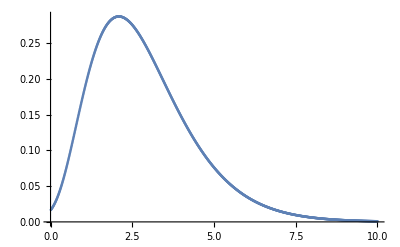

D:\Kut2\MM\hist_jbt.csv

```mathematica
Ht=ILT[Function[s,(5283 (2697921435618318879138+1415747470371442719455 s+266111655551068889800 s^2+17135717804619830500 s^3))/(324821 (2697921435618318879138+3711444161053264098593 s+1589243472478605359255 s^2+276653080728126220300 s^3+17135717804619830500 s^4))+(319 (-77448512645306373686977347927534787570449980029440355618928713765761554-13594853972325116512432257663151608591327986369039188826466253414176295 s+(1496320870056407175566033339940385350643564094012610288245292908058672 (1713160692941178+612004625306375 s+58029775122550 s^2)^4)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^4+(598795029294590024365051223211323174828596834855124595103258343587080 s (1713160692941178+612004625306375 s+58029775122550 s^2)^4)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^4+(59900188181053784802920297355241372700274166395313741885625801559600 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^4)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^4+(12951920060885240744493736002284081098183958777725495663804394824909416 (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3+(12881138519606628862139055543871732746874435388356103347738317412471260 s (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3+(2075536662374253534260589793359843270907402486682215225181844475733400 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3+(308819717443665121686046085365230675711777546325034994995517795923356396 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2+(308358728634056567772763833811914912382285453630675232334163715132220770 s (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2+(48109173749529914036085576459057738935971337343784222514160997741533700 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2-(219603547893676922779453299424898730597235167292332745328638769890562930 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)+(26758806217123535538414982521381082034471669617215446711524801429863365 s (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)+(12358958156659196829483870602865098719389078517308353478605684921978450 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)-(25174790175478677210160389048622392883300781250000000000000000000000000 (2697921435618318879138+1415747470371442719455 s+266111655551068889800 s^2+17135717804619830500 s^3))/(2697921435618318879138+3711444161053264098593 s+1589243472478605359255 s^2+276653080728126220300 s^3+17135717804619830500 s^4)))/472970113672577284784521394549516990570068359375000000000000000000000000+1/9257829923704984444156083750000 107 (180673908015044598048048090398+32997047401616735657709346165 s-(774326764090025050249089141436 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)-(757749791122486738454144668790 s (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)-(121665177540214935411679747300 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)+(539500332515729447974416051038 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)-(52920007462730859635229206315 s (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)-(29997315819651577870644860150 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)+(59567775915176104649287500000 (2697921435618318879138+1415747470371442719455 s+266111655551068889800 s^2+17135717804619830500 s^3))/(2697921435618318879138+3711444161053264098593 s+1589243472478605359255 s^2+276653080728126220300 s^3+17135717804619830500 s^4))+(5471 (117674530851156455210730368436029594612789070500858+20611804939865425156428608104013128320261886875715 s-(20767327153978393588381419398163280522861818136392 (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3)-(20685678019464397665241886622790887743229716260380 s (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3)-(3332231924178297482565808769625021597521235330600 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^3)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^3)-(467059637007005855642145803716635875099193168863920 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)-(466962480641994843382923897116766086059498645000520 s (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)-(72735887815491865590568127258816682317398588636600 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2)^2)/((1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)^2)+(332574940250698739410179583443417998509265916499454 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)-(41023814258438167486136959132243894425252406876235 s (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)-(18738004490786750142207825549102843927510806250650 s^2 (1713160692941178+612004625306375 s+58029775122550 s^2))/(1713160692941178+2003385522298355 s+595941877673800 s^2+52754341020500 s^3)+(38155608336961809295919075408203125000000000000000 (2697921435618318879138+1415747470371442719455 s+266111655551068889800 s^2+17135717804619830500 s^3))/(2697921435618318879138+3711444161053264098593 s+1589243472478605359255 s^2+276653080728126220300 s^3+17135717804619830500 s^4)))/14444921743147169996864487171524414062500000000000000],Table[t,{t,1/100,10,1/100}],60,"cme",100];
Htlist = Table[{i/100,Ht[[i]]},{i,1,1000}];
ListPlot[Htlist]
Export["D:\\Kut2\\MM\\hist_jbt.csv",N[Htlist,6],"Table","FieldSeparator"->","]
```